## Setup

```mathematica
expandParams={x->(c kon)/koff,g->koff/kf};
contractParams={c->koff/kon x,kf->koff/g};
cmap=ColorData[97,"ColorList"];

bigrad=Table[ColorData["ThermometerColors",i],{i,0,1,0.125}];

(* From: https://mathematica.stackexchange.com/questions/174124/extract-colorrange-of-contourplot *)
Clear[legendExtract];
Options[legendExtract]={"RGBasReal"->False};
legendExtract[plot_Legended,OptionsPattern[]]:=Module[{legend=plot[[2,1]],colordata,range,out},(*Extract colorfunction used in plot and the range of values used in the color scaling*){colordata,range}=legend[[1]]/.{b_Blend&:>b[[1]]};
(*Create list of values and colors used in legend*)out={#,ColorData[colordata][Rescale[#,range]]}&/@legend[[2]]/.{{y_Real,_}:>y};
(*If desired,output RGB values as real numbers instead of swatches*)If[OptionValue["RGBasReal"]==True,out/.{RGBColor[vals__]:>vals},out]]

contourcmap=Table[legendExtract[ContourPlot[Min[Cos[x]+Cos[y],1.5],{x,0,4Pi},{y,0,4Pi},PlotLegends->Automatic]][[i,2]],{i,1,7}];
categoricalcmap=ColorData[3,"ColorList"];
```

### Multimers

#### Homodimer

```mathematica
(* Derivation *)
homdimsol=T/.Solve[{Kb==(L R)/B,Kt==(R B)/T,Rt==R+B+2T},{R,B,T}][[2]]//FullSimplify;
HomoDimer[L_,Rt_,Kb_,Kt_]:=(Kt (Kb+L)^2+4 Kb L Rt-(Kb+L) √(Kt (Kt (Kb+L)^2+8 Kb L Rt)))/(8 Kb L);
HomoDimerB[L_,Rt_,Kb_,Kt_]:=(-Kb Kt-Kt L+√(Kt (Kt (Kb+L)^2+8 Kb L Rt)))/(4 Kb);
HomoDiMax[Rt_,Kb_,Kt_]:=(Kb (Kt+Rt)-√(Kb^2 Kt (Kt+2 Rt)))/(2 Kb);

μDi=kp t HomoDimer[c,Rt,koff/kon ,koff/kf];
```

```mathematica
Solve[D[μDi,c]==0,c]
```

{{c→koff/kon}}

```mathematica
Assuming[KD Rt>0,Simplify[μDi/(Rt/2)/.{c->KD,kf->(kon KD)/(g Rt),koff->kon KD}]]
```

-(-1-g+√(g (2+g))) kp t

The Blackwell–Girshick equation tells us that the variance of a sum of a random number N of random variables X_i
 Y=Σ_i^N X_i
is given by:
Var(Y)= E[N]Var(X_0)+Var(N)(E[X_0])^2

For us, these terms have the following analogues:
Var(N)=1/(4/(Rt-HomoDimerB[c,Rt,koff/kon ,koff/kf]-2*HomoDimer[c,Rt,koff/kon ,koff/kf])+1/HomoDimer[c,Rt,koff/kon ,koff/kf])
E[X_0]= kp t
E[N]=HomoDimer[c,Rt,koff/kon ,koff/kf]
Var[X_0]=kp t

```mathematica
VarDi=1/(4/(Rt-HomoDimerB[c,Rt,koff/kon ,koff/kf]-2*HomoDimer[c,Rt,koff/kon ,koff/kf])+1/HomoDimer[c,Rt,koff/kon ,koff/kf]);
ΣDi=μDi+VarDi(kp t)^2;
```

#### Homotrimer

```mathematica
Tri[c_,Rt_,Kb_,Kt_,Kq_]:=(-2 2^(2/3) c^4 Kq^2 (32 Kq^2-144 Kq Kt+135 Kt^2)-3 2^(1/3) √3 √(c^3 Kq^2 Kt (-4 c^3 Kq (Kq-3 Kt) Kt+12 Kb^3 Kq Kt^2+c Kb^2 Kt (-4 Kq^2+243 Rt^2+36 Kq (Kt+3 Rt))-4 c^2 Kb Kq (-9 Kt (Kt+3 Rt)+2 Kq (Kt+4 Rt)))) (9 2^(1/3) Kb Kt+2 (2 c^3 Kq^2 (-8 Kq+27 Kt)+27 c^2 Kb Kq Kt (2 Kq+9 Rt)+9 √3 √(-c^3 Kq^2 Kt (4 c^3 Kq (Kq-3 Kt) Kt-12 Kb^3 Kq Kt^2-c Kb^2 Kt (-4 Kq^2+243 Rt^2+36 Kq (Kt+3 Rt))+4 c^2 Kb Kq (-9 Kt (Kt+3 Rt)+2 Kq (Kt+4 Rt)))))^(1/3))+2^(1/3) c^3 Kq (9 2^(1/3) Kb Kt (32 Kq^2-60 Kq Kt+72 Kq Rt-81 Kt Rt)+2 (16 Kq^2-54 Kq Kt+27 Kt^2) (2 c^3 Kq^2 (-8 Kq+27 Kt)+27 c^2 Kb Kq Kt (2 Kq+9 Rt)+9 √3 √(-c^3 Kq^2 Kt (4 c^3 Kq (Kq-3 Kt) Kt-12 Kb^3 Kq Kt^2-c Kb^2 Kt (-4 Kq^2+243 Rt^2+36 Kq (Kt+3 Rt))+4 c^2 Kb Kq (-9 Kt (Kt+3 Rt)+2 Kq (Kt+4 Rt)))))^(1/3))-c^2 Kq (27 2^(2/3) Kb^2 Kt^2 (10 Kq+27 Rt)-54 2^(1/3) Kb Kt (-2 Kq+2 Kt-3 Rt) (2 c^3 Kq^2 (-8 Kq+27 Kt)+27 c^2 Kb Kq Kt (2 Kq+9 Rt)+9 √3 √(-c^3 Kq^2 Kt (4 c^3 Kq (Kq-3 Kt) Kt-12 Kb^3 Kq Kt^2-c Kb^2 Kt (-4 Kq^2+243 Rt^2+36 Kq (Kt+3 Rt))+4 c^2 Kb Kq (-9 Kt (Kt+3 Rt)+2 Kq (Kt+4 Rt)))))^(1/3)+4 (4 Kq-9 Kt) (2 c^3 Kq^2 (-8 Kq+27 Kt)+27 c^2 Kb Kq Kt (2 Kq+9 Rt)+9 √3 √(-c^3 Kq^2 Kt (4 c^3 Kq (Kq-3 Kt) Kt-12 Kb^3 Kq Kt^2-c Kb^2 Kt (-4 Kq^2+243 Rt^2+36 Kq (Kt+3 Rt))+4 c^2 Kb Kq (-9 Kt (Kt+3 Rt)+2 Kq (Kt+4 Rt)))))^(2/3))+3 c (8 2^(2/3) √3 Kq √(c^3 Kq^2 Kt (-4 c^3 Kq (Kq-3 Kt) Kt+12 Kb^3 Kq Kt^2+c Kb^2 Kt (-4 Kq^2+243 Rt^2+36 Kq (Kt+3 Rt))-4 c^2 Kb Kq (-9 Kt (Kt+3 Rt)+2 Kq (Kt+4 Rt))))-9 2^(2/3) √3 Kt √(c^3 Kq^2 Kt (-4 c^3 Kq (Kq-3 Kt) Kt+12 Kb^3 Kq Kt^2+c Kb^2 Kt (-4 Kq^2+243 Rt^2+36 Kq (Kt+3 Rt))-4 c^2 Kb Kq (-9 Kt (Kt+3 Rt)+2 Kq (Kt+4 Rt))))+18 2^(1/3) Kb^2 Kq Kt^2 (2 c^3 Kq^2 (-8 Kq+27 Kt)+27 c^2 Kb Kq Kt (2 Kq+9 Rt)+9 √3 √(-c^3 Kq^2 Kt (4 c^3 Kq (Kq-3 Kt) Kt-12 Kb^3 Kq Kt^2-c Kb^2 Kt (-4 Kq^2+243 Rt^2+36 Kq (Kt+3 Rt))+4 c^2 Kb Kq (-9 Kt (Kt+3 Rt)+2 Kq (Kt+4 Rt)))))^(1/3)+12 Kb Kq Kt (2 c^3 Kq^2 (-8 Kq+27 Kt)+27 c^2 Kb Kq Kt (2 Kq+9 Rt)+9 √3 √(-c^3 Kq^2 Kt (4 c^3 Kq (Kq-3 Kt) Kt-12 Kb^3 Kq Kt^2-c Kb^2 Kt (-4 Kq^2+243 Rt^2+36 Kq (Kt+3 Rt))+4 c^2 Kb Kq (-9 Kt (Kt+3 Rt)+2 Kq (Kt+4 Rt)))))^(2/3)+18 Kb Kt Rt (2 c^3 Kq^2 (-8 Kq+27 Kt)+27 c^2 Kb Kq Kt (2 Kq+9 Rt)+9 √3 √(-c^3 Kq^2 Kt (4 c^3 Kq (Kq-3 Kt) Kt-12 Kb^3 Kq Kt^2-c Kb^2 Kt (-4 Kq^2+243 Rt^2+36 Kq (Kt+3 Rt))+4 c^2 Kb Kq (-9 Kt (Kt+3 Rt)+2 Kq (Kt+4 Rt)))))^(2/3)))/(162 c Kb Kt (-16 c^3 Kq^3+54 c^3 Kq^2 Kt+54 c^2 Kb Kq^2 Kt+243 c^2 Kb Kq Kt Rt+√(c^3 Kq^2 (4 Kq (-4 c Kq+9 c Kt+9 Kb Kt)^3+c (2 c Kq (-8 Kq+27 Kt)+27 Kb Kt (2 Kq+9 Rt))^2)))^(2/3));


TriRfree[L_,Rt_,Kd_,Γd_,δd_]=-(2 δd)/9-(2^(1/3) (-4 L^2 δd^2+9 L (Kd Γd δd+L Γd δd)))/(9 L (243 Kd L^2 Rt Γd δd+54 Kd L^2 Γd δd^2+54 L^3 Γd δd^2-16 L^3 δd^3+√((243 Kd L^2 Rt Γd δd+54 Kd L^2 Γd δd^2+54 L^3 Γd δd^2-16 L^3 δd^3)^2+4 (-4 L^2 δd^2+9 L (Kd Γd δd+L Γd δd))^3))^(1/3))+1/(9 2^(1/3) L)(243 Kd L^2 Rt Γd δd+54 Kd L^2 Γd δd^2+54 L^3 Γd δd^2-16 L^3 δd^3+√((243 Kd L^2 Rt Γd δd+54 Kd L^2 Γd δd^2+54 L^3 Γd δd^2-16 L^3 δd^3)^2+4 (-4 L^2 δd^2+9 L (Kd Γd δd+L Γd δd))^3))^(1/3);
```

```mathematica
TriMax[Rt_,K1_,K3_,K4_]:=Module[{t1,maxC,c1=Table[10^Logc,{Logc,-16,16,0.1}]},
t1=Table[Tri[c1[[i]],Rt,K1,K3,K4],{i,1,Length[c1]}];
maxC=c1[[Flatten[Position[t1,Max[t1]]][[1]]]];
Tri[maxC,Rt,K1,K3,K4]
]
```

```mathematica
μTri=kp t Tri[c,Rt,koff/kon ,koff/kf,koff/kf];
VarTri=1/(9/TriRfree[c,Rt,koff/kon ,koff/kf,koff/kf]+1/Tri[c,Rt,koff/kon ,koff/kf,koff/kf]);
ΣTri=μTri+(kp t)^2 VarTri;
```

#### Homotetramer

```mathematica
(* Derivation *)
homsoltet=Solve[{
Kb==(c R)/B,
Kt== (B R)/T,
Kq==(T R)/Q,
Ktet==(Q R)/Tet,
Rt==R+B+2T+3Q+4Tet},

{R,B,T,Q,Tet}][[2]];
TetAct[CTEST_,RtTEST_,KbTEST_,KtTEST_,KqTEST_,KtetTEST_]:=Tet/.homsoltet/.{c->CTEST,Rt->RtTEST,Kb->KbTEST,Kt->KtTEST,Kq->KqTEST,Ktet->KtetTEST}


TetMax[Rt_,K1_,K3_,K4_,K5_]:=Module[{t1,maxC,c1=Table[10^Logc,{Logc,-16,16,0.1}]},
t1=Table[TetAct[c1[[i]],Rt,K1,K3,K4,K5],{i,1,Length[c1]}];
maxC=c1[[Flatten[Position[t1,Max[t1]]][[1]]]];
TetAct[maxC,Rt,K1,K3,K4,K5]
]

TetRfree[CTEST_,RtTEST_,KbTEST_,KtTEST_,KqTEST_,KtetTEST_]:=R/.homsoltet/.{c->CTEST,Rt->RtTEST,Kb->KbTEST,Kt->KtTEST,Kq->KqTEST,Ktet->KtetTEST}
```

```mathematica
μTet=kp t TetAct[c,Rt,koff/kon ,koff/kf,koff/kf,koff/kf];

VarTet=1/(16/TetRfree[c,Rt,koff/kon ,koff/kf,koff/kf,koff/kf]+1/TetAct[c,Rt,koff/kon ,koff/kf,koff/kf,koff/kf]);
ΣTet=μTet+(kp t)^2 VarTet;
```

#### Mixed Multimers

These are designed to compare with the adaptive sorting model

```mathematica
DiMixed[c1_,c2_,kofftest_:1,
params_:{R->30000,kon->10^-4,kf->0.09},
tend_:300,δtest_:10]:=Module[{ASeqs,p,sub,L1=c1,L2=c2,sol},
ASeqs={
L1free[t]==L1-(C0[t]+C1[t]),
L2free[t]==L2-(D0[t]+D1[t]),
Rfree[t]==R-(C0[t]+2C1[t]+D0[t]+2D1[t]),
C0'[t]==κ L1free[t]Rfree[t]-(Rfree[t]ϕ+ν1)C0[t],
C1'[t]==ϕ Rfree[t]C0[t]-ν1 C1[t],
D0'[t]==κ L2free[t]Rfree[t]-(Rfree[t]ϕ+ν2)D0[t],
D1'[t]==ϕ Rfree[t]D0[t]-ν2 D1[t],
S[0]==0,C0[0]==0,C1[0]==0,D0[0]==0,D1[0]==0,L1free[0]==L1,L2free[0]==L2,Rfree[0]==R};
p=Join[params,{koff->kofftest,δ->δtest}];
sub={ϕ->kf,ν1->koff,ν2->δ koff,κ->kon};
ASeqs=Evaluate[ASeqs/.sub/.p];
sol=NDSolve[ASeqs,{C1,D1},{t,1,tend}];
(C1[tend]+D1[tend]/.sol)[[1]]
]
TriMixed[c1_,c2_,kofftest_:1,
params_:{R->30000,kon->10^-4,kf->0.09},
tend_:300,δtest_:10]:=Module[{ASeqs,p,sub,L1=c1,L2=c2,sol},
ASeqs={
L1free[t]==L1-(C0[t]+C1[t]+C2[t]),
L2free[t]==L2-(D0[t]+D1[t]+D2[t]),
Rfree[t]==R-(C0[t]+2C1[t]+3C2[t]+D0[t]+2D1[t]+3D2[t]),
C0'[t]==κ L1free[t]Rfree[t]+ν1 C1[t]-(Rfree[t]ϕ+ν1)C0[t],
C1'[t]==ϕ Rfree[t]C0[t]+ν1 C2[t]-(Rfree[t]ϕ+ν1)C1[t],
C2'[t]==ϕ Rfree[t] C1[t]-ν1 C2[t],
D0'[t]==κ L2free[t]Rfree[t]+ν2 D1[t]-(Rfree[t]ϕ+ν2)D0[t],
D1'[t]==ϕ Rfree[t]D0[t]+ν2 D2[t]-(Rfree[t]ϕ+ν2)D1[t],
D2'[t]==ϕ Rfree[t] D1[t]-ν2 D2[t],
S[0]==0,C0[0]==0,C1[0]==0,C2[0]==0,D0[0]==0,D1[0]==0,D2[0]==0,L1free[0]==L1,L2free[0]==L2,Rfree[0]==R};
p=Join[params,{koff->kofftest,δ->δtest}];
sub={ϕ->kf,ν1->koff,ν2->δ koff,κ->kon};
ASeqs=Evaluate[ASeqs/.sub/.p];
sol=NDSolve[ASeqs,{C2,D2},{t,1,tend}];
(C2[tend]+D2[tend]/.sol)[[1]]
]
```

Same ODEs, but now designed for a more traditional parameterization

```mathematica
DiMixedSimple[c1_,c2_,koff1_:1,koff2_,R_,kon_,kf_,
tend_:300]:=Module[{ASeqs,sol},
ASeqs={Rfree[t]==R-C0[t]-2 C1[t]-D0[t]-2 D1[t],
C0'[t]==c1 kon Rfree[t]-C0[t] (koff1+kf Rfree[t]),
C1'[t]==-koff1 C1[t]+kf C0[t] Rfree[t],
D0'[t]==c2 kon Rfree[t]-D0[t] (koff2+kf Rfree[t]),
D1'[t]==-koff2 D1[t]+kf D0[t] Rfree[t],
C0[0]==0,C1[0]==0,D0[0]==0,D1[0]==0,Rfree[0]==R};
sol=Quiet@NDSolve[ASeqs,{C0,D0,Rfree,C1,D1},{t,0,tend}];
Quiet[(C1[tend]+D1[tend]/.sol)]
]
```

#### Non-equilibrium Dimer Model

```mathematica
Solve[{Kb==(L R)/B,Kt E^δ21==(R B)/T,Rt==R+B+2T},{R,B,T}][[2]]//FullSimplify
```

{R→(-ⅇ^δ21 Kt (Kb+L)+√(ⅇ^δ21 Kt (ⅇ^δ21 Kt (Kb+L)^2+8 Kb L Rt)))/(4 L),B→(-ⅇ^δ21 Kt (Kb+L)+√(ⅇ^δ21 Kt (ⅇ^δ21 Kt (Kb+L)^2+8 Kb L Rt)))/(4 Kb),T→(ⅇ^δ21 Kt (Kb+L)^2+4 Kb L Rt-Kb √(ⅇ^δ21 Kt (ⅇ^δ21 Kt (Kb+L)^2+8 Kb L Rt))-L √(ⅇ^δ21 Kt (ⅇ^δ21 Kt (Kb+L)^2+8 Kb L Rt)))/(8 Kb L)}

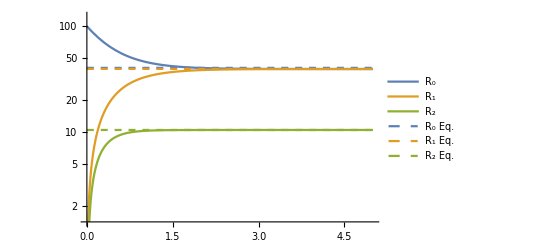

```mathematica
TNonEq[L_,Rt_,Kb_,Kt_,δ21_]:=1/(8 Kb L)(ⅇ^δ21 Kt (Kb+L)^2+4 Kb L Rt-Kb √(ⅇ^δ21 Kt (ⅇ^δ21 Kt (Kb+L)^2+8 Kb L Rt))-L √(ⅇ^δ21 Kt (ⅇ^δ21 Kt (Kb+L)^2+8 Kb L Rt)));
BNonEq[L_,Rt_,Kb_,Kt_,δ21_]:=(-ⅇ^δ21 Kt (Kb+L)+√(ⅇ^δ21 Kt (ⅇ^δ21 Kt (Kb+L)^2+8 Kb L Rt)))/(4 Kb);
RfreeNonEq[L_,Rt_,Kb_,Kt_,δ21_]:=(-ⅇ^δ21 Kt (Kb+L)+√(ⅇ^δ21 Kt (ⅇ^δ21 Kt (Kb+L)^2+8 Kb L Rt)))/(4 L);
DimerNonEqODEs={
D[R2[t],t]==kf R0[t]R1[t]-E^δ21 koff R2[t],
D[R1[t],t]==kon c R0[t]-(koff+kf R0[t])R1[t]+E^δ21 koff R2[t],
R0[t]+R1[t]+2R2[t]==RT,
R0[0]==RT,
R1[0]==0,
R2[0]==0};
DimerNonEqSol[params_]:=NDSolve[Evaluate[DimerNonEqODEs/.params],{R0,R1,R2},{t,100}];

Show[LogPlot[Evaluate[{R0[t],R1[t],R2[t]}/.DimerNonEqSol[{kon->1,c->1,RT->100,koff->1,kf->1,δ21->5}]],{t,0,5},PlotLegends->{"R_0","R_1","R_2"}],
LogPlot[{1+RfreeNonEq[1,100,1,1,5],BNonEq[1,100,1,1,5]+0.1,TNonEq[1,100,1,1,5]},{t,0,5},PlotRange->{Automatic,{0,105}},PlotLegends->{"R_0 Eq.","R_1 Eq.","R_2 Eq."},PlotStyle->Dashed]]
```

```mathematica
μDimerNonEq=kp t TNonEq[c,RT,koff/kon,koff/kf,δ21];
σ2DimerNonEq=μDimerNonEq+(kp t)^2/(4/RfreeNonEq[c,RT,koff/kon,koff/kf,δ21]+1/TNonEq[c,RT,koff/kon,koff/kf,δ21]);
SNRDimerNonEq=μDimerNonEq/(√σ2DimerNonEq)//Simplify;
```

```mathematica
(* Entropy Production *)
PrepDimer={P0->RfreeNonEq[c,RT,koff/kon,koff/kf,δ21]/RT,P1->BNonEq[c,RT,koff/kon,koff/kf,δ21]/RT,P2->TNonEq[c,RT,koff/kon,koff/kf,δ21]/RT};
krepDimer={k01->kon c,k10->koff,k12->E^δ12 kf,k21->kf E^-δ21};
JxyDimer={k01 P0-k10 P1,k12 P1-k21 P2}/.PrepDimer/.krepDimer;
DStotDtDimer=(JxyDimer[[1]]Log[(k01 P0)/(k10 P1)]+JxyDimer[[2]]Log[(k12 P1)/(k21 P2)])/.PrepDimer/.krepDimer;
```

#### Higher N multimers

Chemical equilibrium kinetic equations give that R_i=(kon c)/koff(kf/koff)^(i-1)R0^i 
The conservation equation can be manipulated to solve for R0:
R_T=R0+(Σ_(i=1))^(i=N+1)(kon c)/koff(kf/koff)^(i-1)R0^i

```mathematica
Mult4[kon_,c_,koff_,kf_,RT_]:=Module[{R0ss},
R0ss=R0/.Last[Sort[NSolve[RT==R0+(kon c)/koff R0+(kon c)/koff(kf/koff)R0^2+(kon c)/koff(kf/koff)^2 R0^3+(kon c)/koff(kf/koff)^3 R0^4,R0,Reals]]];
{R0ss,(kon c)/koff R0ss,(kon c)/koff(kf/koff)R0ss^2,(kon c)/koff(kf/koff)^2 R0ss^3,(kon c)/koff(kf/koff)^3 R0ss^4}
]
Mult5[kon_,c_,koff_,kf_,RT_]:=Module[{R0ss},
R0ss=R0/.Last[Sort[NSolve[RT==R0+(kon c)/koff R0+(kon c)/koff(kf/koff)R0^2+(kon c)/koff(kf/koff)^2 R0^3+(kon c)/koff(kf/koff)^3 R0^4+(kon c)/koff(kf/koff)^4 R0^5,R0,Reals]]];
{R0ss,(kon c)/koff R0ss,(kon c)/koff(kf/koff)R0ss^2,(kon c)/koff(kf/koff)^2 R0ss^3,(kon c)/koff(kf/koff)^3 R0ss^4,(kon c)/koff(kf/koff)^4 R0ss^5}
]
Mult6[kon_,c_,koff_,kf_,RT_]:=Module[{R0ss},
R0ss=R0/.Last[Sort[NSolve[RT==R0+(kon c)/koff R0+(kon c)/koff(kf/koff)R0^2+(kon c)/koff(kf/koff)^2 R0^3+(kon c)/koff(kf/koff)^3 R0^4+(kon c)/koff(kf/koff)^4 R0^5+(kon c)/koff(kf/koff)^5 R0^6,R0,Reals]]];
{R0ss,(kon c)/koff R0ss,(kon c)/koff(kf/koff)R0ss^2,(kon c)/koff(kf/koff)^2 R0ss^3,(kon c)/koff(kf/koff)^3 R0ss^4,(kon c)/koff(kf/koff)^4 R0ss^5,(kon c)/koff(kf/koff)^5 R0ss^6}
]
```

```mathematica
MultSNR[Rsol_,kp_,t_,Ns_]:=Module[{μ,VarR,σ},
μ=kp t Last[Rsol];
VarR=(1/Last[Rsol]+(Ns+1)^2/Rsol[[1]])^-1;
σ=√(μ+(kp t)^2 VarR);
μ/σ//N
]
```

### KPR

```mathematica
(* Signal means *)
μ0= kp t x/(1+x)/.expandParams;
μ1= (kp t)/(1+g)x/(1+x)/.expandParams;
μ2=(kp t)/(1+g)^2 x/(1+x)/.expandParams;
μ3=(kp t)/(1+g)^3 x/(1+x)/.expandParams;
μ4=(kp t)/(1+g)^4 x/(1+x)/.expandParams;
μN=(kp t)/(1+g)^Ns x/(1+x)/.expandParams;
```

```mathematica
(* All variances are given for large t *)
(* Signal variances *)
Σ0=(kp t x)/(1+x)+(2 kp^2 t x)/(koff(1+x)^3)/.expandParams;

Σ1=(kp t x ((1+g)^2 koff (1+x)^2+2 kp (1+g^2 (1+x)^2+g (2+x))))/((1+g)^3 koff (1+x)^3)/.expandParams;(*Limit of large t*)

Σ2=(kp t x ((1+g)^3 koff (1+x)^2+2 kp (1+3 g^2 (1+x)^2+g^3 (1+x)^2+g (3+2 x))))/((1+g)^5 koff (1+x)^3)/.expandParams;

Σ3=1/((1+g)^7 koff (1+x)^3)kp t x ((1+g)^4 koff (1+x)^2+2 kp (1+6 g^2 (1+x)^2+4 g^3 (1+x)^2+g^4 (1+x)^2+g (4+3 x)))/.expandParams;

Σ4=1/((1+g)^9 koff (1+x)^3)kp t x ((1+g)^5 koff (1+x)^2+2 kp (1+10 g^2 (1+x)^2+10 g^3 (1+x)^2+5 g^4 (1+x)^2+g^5 (1+x)^2+g (5+4 x)))/.expandParams;
```

```mathematica
ΣN=(kp t x ((1+g)^(Ns+1) koff (1+x)^2+2 kp ((1+g)^(Ns+1) (1+x)^2-x (2+x+g (2+Ns+Ns x+x)))))/((1+g)^(1+2Ns) koff (1+x)^3);
(* (kp t x)/((1+x)(1+g)^Ns)+((2 kp^2 t x)/((koff+koff x)(1+g)^Ns)-(2 kp^2 t x^2 (2+x+g (2+Ns+Ns x+x)))/((1+g)^(1+2Ns) koff (1+x)^3)) *)
```

```mathematica
(* Signal sensitivity *)
η0=(μ0/.koff->δ koff)/μ0;
η1=(μ1/.koff->δ koff)/μ1;
η2=(μ2/.koff->δ koff)/μ2;
η3=(μ3/.koff->δ koff)/μ3;
η4=(μ4/.koff->δ koff)/μ4;
ηN=((kf+koff)^Ns (koff+c kon))/((kf+koff δ)^Ns (c kon+koff δ));
```

```mathematica
(* Estimate variances *)
Σk0=Σ0/D[Evaluate[μ0/.expandParams],koff]^2//Simplify;
Σk1=Σ1/D[Evaluate[μ1/.expandParams],koff]^2//Simplify;
Σk2=Σ2/D[Evaluate[μ2/.expandParams],koff]^2//Simplify;
Σk3=Σ3/D[Evaluate[μ3/.expandParams],koff]^2//Simplify;
Σk4=Σ4/D[Evaluate[μ4/.expandParams],koff]^2//Simplify;
```

#### N=1 Reversible KPR Model

```mathematica
thermoconsistentKPR1eqs={
0==-kon c(1+E^-δ02)R0+koff(R1+R2),
0==kon c R0 -(koff+kf)R1+kf E^-δ21 R2,
0==kf R1-(kf E^-δ21+koff)R2+kon c E^-δ02 R0,
R0+R1+R2==RT};

PssKPR1=({R0/RT,R1/RT,R2/RT}/.Solve[thermoconsistentKPR1eqs,{R0,R1,R2}][[1]])//FullSimplify
```

{(ⅇ^δ02 koff)/(c kon+ⅇ^δ02 (koff+c kon)),(c (kf+ⅇ^δ02 kf+ⅇ^(δ02+δ21) koff) kon)/((kf+ⅇ^δ21 (kf+koff)) (c kon+ⅇ^δ02 (koff+c kon))),(c ⅇ^δ21 (kf+ⅇ^δ02 kf+koff) kon)/((kf+ⅇ^δ21 (kf+koff)) (c kon+ⅇ^δ02 (koff+c kon)))}

```mathematica
PssKPR1[[1]]/PssKPR1[[2]]/.{δ02->0,δ21->0}//Simplify
PssKPR1[[1]]/PssKPR1[[3]]/.{δ02->0,δ21->0}//Simplify
```

koff/(c kon)

koff/(c kon)

```mathematica
R0KPR1[c_,kon_,koff_,kf_,δ21_,δ02_,RT_]=(E^δ02 koff RT)/(c kon+E^δ02 (koff+c kon));
R1KPR1[c_,kon_,koff_,kf_,δ21_,δ02_,RT_]=(c (kf+E^δ02 kf+E^(δ02+δ21) koff) kon RT)/((kf+E^δ21 (kf+koff)) (c kon+E^δ02 (koff+c kon)));
R2KPR1[c_,kon_,koff_,kf_,δ21_,δ02_,RT_]=(c E^δ21 (kf+E^δ02 kf+koff) kon RT)/((kf+E^δ21 (kf+koff)) (c kon+E^δ02 (koff+c kon)));
```

```mathematica
KPR1ODEs={
D[R2[t],t]==kf R1[t]-(kf E^-δ21+koff)R2[t]+kon c E^-δ02 R0[t],
D[R1[t],t]==kon c R0[t] -(koff+kf)R1[t]+kf E^-δ21 R2[t],
R0[t]+R1[t]+R2[t]==RT,
R0[0]==RT,
R1[0]==0,
R2[0]==0};
KPR1Sol[params_]:=NDSolve[Evaluate[KPR1ODEs/.params],{R0,R1,R2},{t,100}];
```

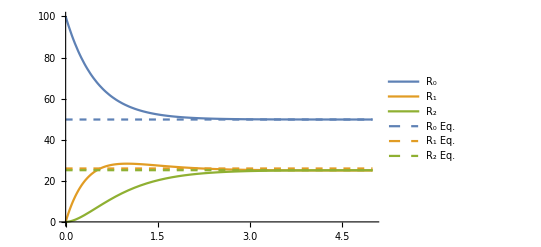

```mathematica
Show[Plot[Evaluate[{R0[t],R1[t],R2[t]}/.KPR1Sol[{kon->1,c->1,RT->100,koff->1,kf->1,δ02->5,δ21->5}]],{t,0,5},PlotLegends->{"R_0","R_1","R_2"}],
Plot[{R0KPR1[1,1,1,1,5,5,100],R1KPR1[1,1,1,1,5,5,100]+1,R2KPR1[1,1,1,1,5,5,100]},{t,0,5},PlotRange->{Automatic,{0,105}},PlotLegends->{"R_0 Eq.","R_1 Eq.","R_2 Eq."},PlotStyle->Dashed]]
```

```mathematica
expandParams={x->(kon c)/koff,g->koff/kf};
KPR1Eq=1/(1+g)x/(1+x)/.expandParams;
μN1=kp t KPR1Eq;
σ2N1=(kp t x ((1+g)^2 koff (1+x)^2+2 kp (1+g^2 (1+x)^2+g (2+x))))/((1+g)^3 koff (1+x)^3)/.expandParams;
```

```mathematica
μN1NonEq=kp t R2KPR1[c,kon,koff,kf,δ21,δ02,RT];
```

```mathematica
(* Entropy Production *)
PrepKPR1={P0->PssKPR1[[1]],P1->PssKPR1[[2]],P2->PssKPR1[[3]]};
krepKPR1={k01->kon c,k10->koff,k02->kon c E^-δ02,k20->koff,k12->kf,k21->kf E^-δ21};
JxyKPR1={k01 P0-k10 P1,k02 P0-k20 P2,k12 P1-k21 P2}/.PrepKPR1/.krepKPR1;
DStotDtKPR1=(JxyKPR1[[1]]Log[(k01 P0)/(k10 P1)]+JxyKPR1[[2]]Log[(k02 P0)/(k20 P2)]+JxyKPR1[[3]]Log[(k12 P1)/(k21 P2)])/.PrepKPR1/.krepKPR1;
```

#### Variance for N=1 Reversible KPR model

```mathematica
σ2N1NonEq=kp (1/(c ν+ⅇ^(δ02/kT) (koff+c ν))ⅇ^(δ02/kT) koff ((c kf r0 t ν)/(kf koff r0+ⅇ^(-δ21/kT) kf koff r0+koff^2 r0^2+c kf r0 ν+c ⅇ^(-δ02/kT) kf r0 ν+c ⅇ^(-δ21/kT) kf r0 ν+c ⅇ^(-δ02/kT-δ21/kT) kf r0 ν+c koff r0^2 ν+c ⅇ^(-δ02/kT) koff r0^2 ν)+(c ⅇ^(-δ02/kT) kf r0 t ν)/(kf koff r0+ⅇ^(-δ21/kT) kf koff r0+koff^2 r0^2+c kf r0 ν+c ⅇ^(-δ02/kT) kf r0 ν+c ⅇ^(-δ21/kT) kf r0 ν+c ⅇ^(-δ02/kT-δ21/kT) kf r0 ν+c koff r0^2 ν+c ⅇ^(-δ02/kT) koff r0^2 ν)+(c ⅇ^(-δ02/kT) koff r0^2 t ν)/(kf koff r0+ⅇ^(-δ21/kT) kf koff r0+koff^2 r0^2+c kf r0 ν+c ⅇ^(-δ02/kT) kf r0 ν+c ⅇ^(-δ21/kT) kf r0 ν+c ⅇ^(-δ02/kT-δ21/kT) kf r0 ν+c koff r0^2 ν+c ⅇ^(-δ02/kT) koff r0^2 ν)+(2 c ⅇ^((δ02+2 δ21)/kT) (-1+ⅇ^(1/2 t (-kf-ⅇ^(-δ21/kT) kf-2 koff r0-c r0 ν-c ⅇ^(-δ02/kT) r0 ν+√(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2)))) r0 ν (-ⅇ^(δ02/kT) kf+ⅇ^((δ02+δ21)/kT) kf+2 ⅇ^((2 δ02+δ21)/kT) kf-c ⅇ^(δ21/kT) r0 ν-c ⅇ^((δ02+δ21)/kT) r0 ν+ⅇ^((δ02+δ21)/kT) √(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2)))/((ⅇ^(δ02/kT) kf+ⅇ^((δ02+δ21)/kT) kf+2 ⅇ^((δ02+δ21)/kT) koff r0+c ⅇ^(δ21/kT) r0 ν+c ⅇ^((δ02+δ21)/kT) r0 ν-ⅇ^((δ02+δ21)/kT) √(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2)) (-ⅇ^((2 δ02)/kT) kf^2-ⅇ^((2 (δ02+δ21))/kT) kf^2-2 ⅇ^((2 δ02+δ21)/kT) kf^2+2 c ⅇ^((δ02+δ21)/kT) kf r0 ν+2 c ⅇ^((2 (δ02+δ21))/kT) kf r0 ν+2 c ⅇ^((2 δ02+δ21)/kT) kf r0 ν+2 c ⅇ^((δ02+2 δ21)/kT) kf r0 ν-c^2 ⅇ^((2 δ21)/kT) r0^2 ν^2-c^2 ⅇ^((2 (δ02+δ21))/kT) r0^2 ν^2-2 c^2 ⅇ^((δ02+2 δ21)/kT) r0^2 ν^2+ⅇ^((2 (δ02+δ21))/kT) kf √(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2)+ⅇ^((2 δ02+δ21)/kT) kf √(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2)+2 ⅇ^((2 (δ02+δ21))/kT) koff r0 √(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2)+c ⅇ^((2 (δ02+δ21))/kT) r0 ν √(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2)+c ⅇ^((δ02+2 δ21)/kT) r0 ν √(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2)))+(2 c ⅇ^(δ02/kT+(2 δ21)/kT-1/2 ⅇ^(-(δ02+δ21)/kT) t (ⅇ^(δ02/kT) kf+c ⅇ^(δ21/kT) r0 ν+ⅇ^((δ02+δ21)/kT) (kf+2 koff r0+c r0 ν+√(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2)))) (-1+ⅇ^(1/2 ⅇ^(-(δ02+δ21)/kT) t (ⅇ^(δ02/kT) kf+c ⅇ^(δ21/kT) r0 ν+ⅇ^((δ02+δ21)/kT) (kf+2 koff r0+c r0 ν+√(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2))))) r0 ν (-ⅇ^(δ02/kT) kf+ⅇ^((δ02+δ21)/kT) kf+2 ⅇ^((2 δ02+δ21)/kT) kf-c ⅇ^(δ21/kT) r0 ν-c ⅇ^((δ02+δ21)/kT) r0 ν-ⅇ^((δ02+δ21)/kT) √(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2)))/((ⅇ^(δ02/kT) kf+ⅇ^((δ02+δ21)/kT) kf+2 ⅇ^((δ02+δ21)/kT) koff r0+c ⅇ^(δ21/kT) r0 ν+c ⅇ^((δ02+δ21)/kT) r0 ν+ⅇ^((δ02+δ21)/kT) √(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2)) (ⅇ^((2 δ02)/kT) kf^2+ⅇ^((2 (δ02+δ21))/kT) kf^2+2 ⅇ^((2 δ02+δ21)/kT) kf^2-2 c ⅇ^((δ02+δ21)/kT) kf r0 ν-2 c ⅇ^((2 (δ02+δ21))/kT) kf r0 ν-2 c ⅇ^((2 δ02+δ21)/kT) kf r0 ν-2 c ⅇ^((δ02+2 δ21)/kT) kf r0 ν+c^2 ⅇ^((2 δ21)/kT) r0^2 ν^2+c^2 ⅇ^((2 (δ02+δ21))/kT) r0^2 ν^2+2 c^2 ⅇ^((δ02+2 δ21)/kT) r0^2 ν^2+ⅇ^((2 (δ02+δ21))/kT) kf √(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2)+ⅇ^((2 δ02+δ21)/kT) kf √(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2)+2 ⅇ^((2 (δ02+δ21))/kT) koff r0 √(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2)+c ⅇ^((2 (δ02+δ21))/kT) r0 ν √(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2)+c ⅇ^((δ02+2 δ21)/kT) r0 ν √(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2))))+(c ⅇ^(δ21/kT) (kf+ⅇ^(δ02/kT) kf+koff r0) ν ((c kf r0 t ν)/(kf koff r0+ⅇ^(-δ21/kT) kf koff r0+koff^2 r0^2+c kf r0 ν+c ⅇ^(-δ02/kT) kf r0 ν+c ⅇ^(-δ21/kT) kf r0 ν+c ⅇ^(-δ02/kT-δ21/kT) kf r0 ν+c koff r0^2 ν+c ⅇ^(-δ02/kT) koff r0^2 ν)+(c ⅇ^(-δ02/kT) kf r0 t ν)/(kf koff r0+ⅇ^(-δ21/kT) kf koff r0+koff^2 r0^2+c kf r0 ν+c ⅇ^(-δ02/kT) kf r0 ν+c ⅇ^(-δ21/kT) kf r0 ν+c ⅇ^(-δ02/kT-δ21/kT) kf r0 ν+c koff r0^2 ν+c ⅇ^(-δ02/kT) koff r0^2 ν)+(c ⅇ^(-δ02/kT) koff r0^2 t ν)/(kf koff r0+ⅇ^(-δ21/kT) kf koff r0+koff^2 r0^2+c kf r0 ν+c ⅇ^(-δ02/kT) kf r0 ν+c ⅇ^(-δ21/kT) kf r0 ν+c ⅇ^(-δ02/kT-δ21/kT) kf r0 ν+c koff r0^2 ν+c ⅇ^(-δ02/kT) koff r0^2 ν)-(2 ⅇ^((2 δ02+δ21)/kT) (-1+ⅇ^(1/2 t (-kf-ⅇ^(-δ21/kT) kf-2 koff r0-c r0 ν-c ⅇ^(-δ02/kT) r0 ν+√(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2)))) (-ⅇ^(δ02/kT) kf^2-ⅇ^((δ02+δ21)/kT) kf^2-ⅇ^((δ02+δ21)/kT) kf koff r0+ⅇ^((δ02+2 δ21)/kT) kf koff r0+c ⅇ^(δ21/kT) kf r0 ν+c ⅇ^((δ02+δ21)/kT) kf r0 ν-c ⅇ^((2 δ21)/kT) koff r0^2 ν+c ⅇ^((δ02+2 δ21)/kT) koff r0^2 ν+ⅇ^((δ02+δ21)/kT) kf √(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2)+ⅇ^((δ02+2 δ21)/kT) koff r0 √(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2)))/((ⅇ^(δ02/kT) kf+ⅇ^((δ02+δ21)/kT) kf+2 ⅇ^((δ02+δ21)/kT) koff r0+c ⅇ^(δ21/kT) r0 ν+c ⅇ^((δ02+δ21)/kT) r0 ν-ⅇ^((δ02+δ21)/kT) √(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2)) (-ⅇ^((2 δ02)/kT) kf^2-ⅇ^((2 (δ02+δ21))/kT) kf^2-2 ⅇ^((2 δ02+δ21)/kT) kf^2+2 c ⅇ^((δ02+δ21)/kT) kf r0 ν+2 c ⅇ^((2 (δ02+δ21))/kT) kf r0 ν+2 c ⅇ^((2 δ02+δ21)/kT) kf r0 ν+2 c ⅇ^((δ02+2 δ21)/kT) kf r0 ν-c^2 ⅇ^((2 δ21)/kT) r0^2 ν^2-c^2 ⅇ^((2 (δ02+δ21))/kT) r0^2 ν^2-2 c^2 ⅇ^((δ02+2 δ21)/kT) r0^2 ν^2+ⅇ^((2 (δ02+δ21))/kT) kf √(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2)+ⅇ^((2 δ02+δ21)/kT) kf √(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2)+2 ⅇ^((2 (δ02+δ21))/kT) koff r0 √(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2)+c ⅇ^((2 (δ02+δ21))/kT) r0 ν √(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2)+c ⅇ^((δ02+2 δ21)/kT) r0 ν √(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2)))+(2 ⅇ^((2 δ02)/kT+δ21/kT-1/2 ⅇ^(-(δ02+δ21)/kT) t (ⅇ^(δ02/kT) kf+c ⅇ^(δ21/kT) r0 ν+ⅇ^((δ02+δ21)/kT) (kf+2 koff r0+c r0 ν+√(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2)))) (-1+ⅇ^(1/2 ⅇ^(-(δ02+δ21)/kT) t (ⅇ^(δ02/kT) kf+c ⅇ^(δ21/kT) r0 ν+ⅇ^((δ02+δ21)/kT) (kf+2 koff r0+c r0 ν+√(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2))))) (ⅇ^(δ02/kT) kf^2+ⅇ^((δ02+δ21)/kT) kf^2+ⅇ^((δ02+δ21)/kT) kf koff r0-ⅇ^((δ02+2 δ21)/kT) kf koff r0-c ⅇ^(δ21/kT) kf r0 ν-c ⅇ^((δ02+δ21)/kT) kf r0 ν+c ⅇ^((2 δ21)/kT) koff r0^2 ν-c ⅇ^((δ02+2 δ21)/kT) koff r0^2 ν+ⅇ^((δ02+δ21)/kT) kf √(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2)+ⅇ^((δ02+2 δ21)/kT) koff r0 √(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2)))/((ⅇ^(δ02/kT) kf+ⅇ^((δ02+δ21)/kT) kf+2 ⅇ^((δ02+δ21)/kT) koff r0+c ⅇ^(δ21/kT) r0 ν+c ⅇ^((δ02+δ21)/kT) r0 ν+ⅇ^((δ02+δ21)/kT) √(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2)) (ⅇ^((2 δ02)/kT) kf^2+ⅇ^((2 (δ02+δ21))/kT) kf^2+2 ⅇ^((2 δ02+δ21)/kT) kf^2-2 c ⅇ^((δ02+δ21)/kT) kf r0 ν-2 c ⅇ^((2 (δ02+δ21))/kT) kf r0 ν-2 c ⅇ^((2 δ02+δ21)/kT) kf r0 ν-2 c ⅇ^((δ02+2 δ21)/kT) kf r0 ν+c^2 ⅇ^((2 δ21)/kT) r0^2 ν^2+c^2 ⅇ^((2 (δ02+δ21))/kT) r0^2 ν^2+2 c^2 ⅇ^((δ02+2 δ21)/kT) r0^2 ν^2+ⅇ^((2 (δ02+δ21))/kT) kf √(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2)+ⅇ^((2 δ02+δ21)/kT) kf √(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2)+2 ⅇ^((2 (δ02+δ21))/kT) koff r0 √(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2)+c ⅇ^((2 (δ02+δ21))/kT) r0 ν √(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2)+c ⅇ^((δ02+2 δ21)/kT) r0 ν √(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2)))))/((kf+ⅇ^(δ21/kT) kf+ⅇ^(δ21/kT) koff r0) (c ν+ⅇ^(δ02/kT) (koff+c ν)))+(c (kf+ⅇ^(δ02/kT) kf+ⅇ^((δ02+δ21)/kT) koff r0) ν ((c kf r0 t ν)/(kf koff r0+ⅇ^(-δ21/kT) kf koff r0+koff^2 r0^2+c kf r0 ν+c ⅇ^(-δ02/kT) kf r0 ν+c ⅇ^(-δ21/kT) kf r0 ν+c ⅇ^(-δ02/kT-δ21/kT) kf r0 ν+c koff r0^2 ν+c ⅇ^(-δ02/kT) koff r0^2 ν)+(c ⅇ^(-δ02/kT) kf r0 t ν)/(kf koff r0+ⅇ^(-δ21/kT) kf koff r0+koff^2 r0^2+c kf r0 ν+c ⅇ^(-δ02/kT) kf r0 ν+c ⅇ^(-δ21/kT) kf r0 ν+c ⅇ^(-δ02/kT-δ21/kT) kf r0 ν+c koff r0^2 ν+c ⅇ^(-δ02/kT) koff r0^2 ν)+(c ⅇ^(-δ02/kT) koff r0^2 t ν)/(kf koff r0+ⅇ^(-δ21/kT) kf koff r0+koff^2 r0^2+c kf r0 ν+c ⅇ^(-δ02/kT) kf r0 ν+c ⅇ^(-δ21/kT) kf r0 ν+c ⅇ^(-δ02/kT-δ21/kT) kf r0 ν+c koff r0^2 ν+c ⅇ^(-δ02/kT) koff r0^2 ν)-(2 ⅇ^((2 δ02)/kT+(2 δ21)/kT-1/2 ⅇ^(-(δ02+δ21)/kT) t (ⅇ^(δ02/kT) kf+c ⅇ^(δ21/kT) r0 ν+ⅇ^((δ02+δ21)/kT) (kf+2 koff r0+c r0 ν+√(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2)))) (-1+ⅇ^(1/2 ⅇ^(-(δ02+δ21)/kT) t (ⅇ^(δ02/kT) kf+c ⅇ^(δ21/kT) r0 ν+ⅇ^((δ02+δ21)/kT) (kf+2 koff r0+c r0 ν+√(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2))))) (ⅇ^(δ02/kT) kf^2-c ⅇ^(δ21/kT) r0 (kf+2 koff r0) ν+ⅇ^((δ02+δ21)/kT) kf (kf+2 koff r0-c r0 ν+√(ⅇ^(-(2 (δ02+δ21))/kT) (ⅇ^(δ02/kT) kf-c ⅇ^(δ21/kT) r0 ν+ⅇ^((δ02+δ21)/kT) (kf-c r0 ν))^2))))/((ⅇ^(δ02/kT) kf+ⅇ^((δ02+δ21)/kT) kf+2 ⅇ^((δ02+δ21)/kT) koff r0+c ⅇ^(δ21/kT) r0 ν+c ⅇ^((δ02+δ21)/kT) r0 ν+ⅇ^((δ02+δ21)/kT) √(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2)) (ⅇ^((2 δ02)/kT) kf^2+ⅇ^((2 (δ02+δ21))/kT) kf^2+2 ⅇ^((2 δ02+δ21)/kT) kf^2-2 c ⅇ^((δ02+δ21)/kT) kf r0 ν-2 c ⅇ^((2 (δ02+δ21))/kT) kf r0 ν-2 c ⅇ^((2 δ02+δ21)/kT) kf r0 ν-2 c ⅇ^((δ02+2 δ21)/kT) kf r0 ν+c^2 ⅇ^((2 δ21)/kT) r0^2 ν^2+c^2 ⅇ^((2 (δ02+δ21))/kT) r0^2 ν^2+2 c^2 ⅇ^((δ02+2 δ21)/kT) r0^2 ν^2+ⅇ^((2 (δ02+δ21))/kT) kf √(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2)+ⅇ^((2 δ02+δ21)/kT) kf √(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2)+2 ⅇ^((2 (δ02+δ21))/kT) koff r0 √(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2)+c ⅇ^((2 (δ02+δ21))/kT) r0 ν √(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2)+c ⅇ^((δ02+2 δ21)/kT) r0 ν √(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2)))+(2 ⅇ^((2 (δ02+δ21))/kT) (-1+ⅇ^(1/2 t (-kf-ⅇ^(-δ21/kT) kf-2 koff r0-c r0 ν-c ⅇ^(-δ02/kT) r0 ν+√(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2)))) (-ⅇ^(δ02/kT) kf^2+c ⅇ^(δ21/kT) r0 (kf+2 koff r0) ν+ⅇ^((δ02+δ21)/kT) kf (-kf-2 koff r0+c r0 ν+√(ⅇ^(-(2 (δ02+δ21))/kT) (ⅇ^(δ02/kT) kf-c ⅇ^(δ21/kT) r0 ν+ⅇ^((δ02+δ21)/kT) (kf-c r0 ν))^2))))/((ⅇ^(δ02/kT) kf+ⅇ^((δ02+δ21)/kT) kf+2 ⅇ^((δ02+δ21)/kT) koff r0+c ⅇ^(δ21/kT) r0 ν+c ⅇ^((δ02+δ21)/kT) r0 ν-ⅇ^((δ02+δ21)/kT) √(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2)) (-ⅇ^((2 δ02)/kT) kf^2-ⅇ^((2 (δ02+δ21))/kT) kf^2-2 ⅇ^((2 δ02+δ21)/kT) kf^2+2 c ⅇ^((δ02+δ21)/kT) kf r0 ν+2 c ⅇ^((2 (δ02+δ21))/kT) kf r0 ν+2 c ⅇ^((2 δ02+δ21)/kT) kf r0 ν+2 c ⅇ^((δ02+2 δ21)/kT) kf r0 ν-c^2 ⅇ^((2 δ21)/kT) r0^2 ν^2-c^2 ⅇ^((2 (δ02+δ21))/kT) r0^2 ν^2-2 c^2 ⅇ^((δ02+2 δ21)/kT) r0^2 ν^2+ⅇ^((2 (δ02+δ21))/kT) kf √(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2)+ⅇ^((2 δ02+δ21)/kT) kf √(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2)+2 ⅇ^((2 (δ02+δ21))/kT) koff r0 √(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2)+c ⅇ^((2 (δ02+δ21))/kT) r0 ν √(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2)+c ⅇ^((δ02+2 δ21)/kT) r0 ν √(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2)))))/((kf+ⅇ^(δ21/kT) kf+ⅇ^(δ21/kT) koff r0) (c ν+ⅇ^(δ02/kT) (koff+c ν))))+kp^2 (-(c^2 ⅇ^((2 δ21)/kT) (kf+ⅇ^(δ02/kT) kf+koff r0)^2 t^2 ν^2)/((kf+ⅇ^(δ21/kT) kf+ⅇ^(δ21/kT) koff r0)^2 (c ν+ⅇ^(δ02/kT) (koff+c ν))^2)+2 ((c ⅇ^(δ21/kT) (kf+ⅇ^(δ02/kT) kf+koff r0) t^2 ν)/(2 (kf+ⅇ^(δ21/kT) (kf+koff r0)) (c ν+ⅇ^(δ02/kT) (koff+c ν)))-(2 ⅇ^((δ02+δ21)/kT) (-t-(2 ⅇ^((δ02+δ21)/kT) (-1+ⅇ^(1/2 t (-kf-ⅇ^(-δ21/kT) kf-2 koff r0-c r0 ν-c ⅇ^(-δ02/kT) r0 ν+√(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2)))))/(ⅇ^(δ02/kT) kf+ⅇ^((δ02+δ21)/kT) kf+2 ⅇ^((δ02+δ21)/kT) koff r0+c ⅇ^(δ21/kT) r0 ν+c ⅇ^((δ02+δ21)/kT) r0 ν-ⅇ^((δ02+δ21)/kT) √(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2))) (ⅇ^(-δ21/kT) kf^2+c ⅇ^(-δ02/kT) koff r0^2 ν-1/2 ⅇ^(-(δ02+2 δ21)/kT) (kf+ⅇ^(δ21/kT) koff r0) (-ⅇ^(δ02/kT) kf+c ⅇ^(δ21/kT) r0 ν+ⅇ^((δ02+δ21)/kT) (kf+c r0 ν+√(ⅇ^(-(2 (δ02+δ21))/kT) (ⅇ^(δ02/kT) kf-c ⅇ^(δ21/kT) r0 ν+ⅇ^((δ02+δ21)/kT) (kf-c r0 ν))^2)))))/((ⅇ^(δ02/kT) kf+ⅇ^((δ02+δ21)/kT) kf+2 ⅇ^((δ02+δ21)/kT) koff r0+c ⅇ^(δ21/kT) r0 ν+c ⅇ^((δ02+δ21)/kT) r0 ν-ⅇ^((δ02+δ21)/kT) √(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2)) (kf koff r0+ⅇ^(-δ21/kT) kf koff r0+koff^2 r0^2+c kf r0 ν+c ⅇ^(-δ02/kT) kf r0 ν+c ⅇ^(-δ21/kT) kf r0 ν+c ⅇ^(-(δ02+δ21)/kT) kf r0 ν+c koff r0^2 ν+c ⅇ^(-δ02/kT) koff r0^2 ν-ⅇ^(-(2 (δ02+δ21))/kT) (ⅇ^(δ02/kT) kf+c ⅇ^(δ21/kT) r0 ν+ⅇ^((δ02+δ21)/kT) (kf+2 koff r0+c r0 ν)) (ⅇ^(δ02/kT) kf+c ⅇ^(δ21/kT) r0 ν+ⅇ^((δ02+δ21)/kT) (kf+2 koff r0+c r0 ν-√(ⅇ^(-(2 (δ02+δ21))/kT) (ⅇ^(δ02/kT) kf-c ⅇ^(δ21/kT) r0 ν+ⅇ^((δ02+δ21)/kT) (kf-c r0 ν))^2)))+3/4 ⅇ^(-(2 (δ02+δ21))/kT) (ⅇ^(δ02/kT) kf+c ⅇ^(δ21/kT) r0 ν+ⅇ^((δ02+δ21)/kT) (kf+2 koff r0+c r0 ν-√(ⅇ^(-(2 (δ02+δ21))/kT) (ⅇ^(δ02/kT) kf-c ⅇ^(δ21/kT) r0 ν+ⅇ^((δ02+δ21)/kT) (kf-c r0 ν))^2)))^2))+(2 ⅇ^((δ02+δ21)/kT) (t+(2 ⅇ^((δ02+δ21)/kT) (-1+ⅇ^(-1/2 ⅇ^(-(δ02+δ21)/kT) t (ⅇ^(δ02/kT) kf+c ⅇ^(δ21/kT) r0 ν+ⅇ^((δ02+δ21)/kT) (kf+2 koff r0+c r0 ν+√(ⅇ^(-(2 (δ02+δ21))/kT) (ⅇ^(δ02/kT) kf-c ⅇ^(δ21/kT) r0 ν+ⅇ^((δ02+δ21)/kT) (kf-c r0 ν))^2))))))/(ⅇ^(δ02/kT) kf+ⅇ^((δ02+δ21)/kT) kf+2 ⅇ^((δ02+δ21)/kT) koff r0+c ⅇ^(δ21/kT) r0 ν+c ⅇ^((δ02+δ21)/kT) r0 ν+ⅇ^((δ02+δ21)/kT) √(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2))) (ⅇ^(-δ21/kT) kf^2+c ⅇ^(-δ02/kT) koff r0^2 ν-1/2 ⅇ^(-(δ02+2 δ21)/kT) (kf+ⅇ^(δ21/kT) koff r0) (-ⅇ^(δ02/kT) kf+c ⅇ^(δ21/kT) r0 ν+ⅇ^((δ02+δ21)/kT) (kf+c r0 ν-√(ⅇ^(-(2 (δ02+δ21))/kT) (ⅇ^(δ02/kT) kf-c ⅇ^(δ21/kT) r0 ν+ⅇ^((δ02+δ21)/kT) (kf-c r0 ν))^2)))))/((ⅇ^(δ02/kT) kf+ⅇ^((δ02+δ21)/kT) kf+2 ⅇ^((δ02+δ21)/kT) koff r0+c ⅇ^(δ21/kT) r0 ν+c ⅇ^((δ02+δ21)/kT) r0 ν+ⅇ^((δ02+δ21)/kT) √(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2)) (kf koff r0+ⅇ^(-δ21/kT) kf koff r0+koff^2 r0^2+c kf r0 ν+c ⅇ^(-δ02/kT) kf r0 ν+c ⅇ^(-δ21/kT) kf r0 ν+c ⅇ^(-(δ02+δ21)/kT) kf r0 ν+c koff r0^2 ν+c ⅇ^(-δ02/kT) koff r0^2 ν-ⅇ^(-(2 (δ02+δ21))/kT) (ⅇ^(δ02/kT) kf+c ⅇ^(δ21/kT) r0 ν+ⅇ^((δ02+δ21)/kT) (kf+2 koff r0+c r0 ν)) (ⅇ^(δ02/kT) kf+c ⅇ^(δ21/kT) r0 ν+ⅇ^((δ02+δ21)/kT) (kf+2 koff r0+c r0 ν+√(ⅇ^(-(2 (δ02+δ21))/kT) (ⅇ^(δ02/kT) kf-c ⅇ^(δ21/kT) r0 ν+ⅇ^((δ02+δ21)/kT) (kf-c r0 ν))^2)))+3/4 ⅇ^(-(2 (δ02+δ21))/kT) (ⅇ^(δ02/kT) kf+c ⅇ^(δ21/kT) r0 ν+ⅇ^((δ02+δ21)/kT) (kf+2 koff r0+c r0 ν+√(ⅇ^(-(2 (δ02+δ21))/kT) (ⅇ^(δ02/kT) kf-c ⅇ^(δ21/kT) r0 ν+ⅇ^((δ02+δ21)/kT) (kf-c r0 ν))^2)))^2))));
```

```mathematica
σ2N1NonEq=σ2N1NonEq/.{r0->1,ν->kon,kT->1};
```

#### Mixed Ligands for KPR 1

```mathematica
mixedLigandsKPR1eqs={
0==-(kon c1+kon c2) P0+koff1(P1a+P2a)+koff2(P1b+P2b),
0==kon c1 P0-(koff1+kf)P1a,
0==kf P1a-koff1 P2a,
0==kon c2 P0-(koff2+kf)P1b,
(*0==kf P1b-koff2 P2b*)
P0+P1a+P2a+P1b+P2b==1};
mixedKPR={P0,P1a,P2a,P1b,P2b}/.Solve[mixedLigandsKPR1eqs,{P0,P1a,P2a,P1b,P2b}][[1]]
```

{(koff1 koff2)/(koff1 koff2+c2 koff1 kon+c1 koff2 kon),(c1 koff1 koff2 kon)/((kf+koff1) (koff1 koff2+c2 koff1 kon+c1 koff2 kon)),(c1 kf koff2 kon)/((kf+koff1) (koff1 koff2+c2 koff1 kon+c1 koff2 kon)),(c2 koff1 koff2 kon)/((kf+koff2) (koff1 koff2+c2 koff1 kon+c1 koff2 kon)),(c2 kf koff1 kon)/((kf+koff2) (koff1 koff2+c2 koff1 kon+c1 koff2 kon))}

### Adaptive Sorting

Taken from Francois and Altan-Bonnet (2016), Journal of Statistical Physics
-Graphics-
To map this model to the other models we consider here, relabel ϕ→ k_f and τ→k_off^-1 (ν1→k_off)

In the non-saturated receptor regime, we use the approximation provided from the above cited paper:

```mathematica
ASResponse[c1_,c2_,kofftest_:1,
params_:{R->30000,kon->10^-4,kf->0.09,b->0.04,γ->1.2*10^-6,St->600000,α->0.05,β->25},
tend_:300]:=Module[{ASeqs,p,sub,L1=c1,L2=c2,δtest=10,sol},
ASeqs={
S'[t]==α(C1[t]+D1[t])(St-S[t])-β S[t],
C0'[t]==κ(L1-(C0[t]+C1[t]+C2[t]))(R-(C0[t]+C1[t]+C2[t]+D0[t]+D1[t]+D2[t]))+(b+γ S[t])C1[t]-(ϕ+ν1)C0[t],
C1'[t]==ϕ C0[t]+(b+γ S[t])C2[t]-(ϕ+b+γ S[t]+ν1)C1[t],
C2'[t]==ϕ C1[t]-(b+γ S[t]+ν1)C2[t],
D0'[t]==κ(L2-(D0[t]+D1[t]+D2[t]))(R-(C0[t]+C1[t]+C2[t]+D0[t]+D1[t]+D2[t]))+(b+γ S[t])D1[t]-(ϕ+ν2)D0[t],
D1'[t]==ϕ D0[t]+(b+γ S[t])D2[t]-(ϕ+b+γ S[t]+ν2)D1[t],
D2'[t]==ϕ D1[t]-(b+γ S[t]+ν2)D2[t],
S[0]==0,C0[0]==0,C1[0]==0,C2[0]==0,D0[0]==0,D1[0]==0,D2[0]==0};
p=Join[params,{koff->kofftest,δ->δtest}];
sub={ϕ->kf,ν1->koff,ν2->δ koff,κ->kon};
ASeqs=Evaluate[ASeqs/.sub/.p];
sol=NDSolve[ASeqs,C2,{t,1,tend}];
(C2[tend]/.sol)[[1]]
]
```

```mathematica
AS5[c1_,c2_,kofftest_:1,
params_:{R->30000,kon->10^-4,kf->0.09,b->0.04,γ->1.2*10^-6,St->600000,α->0.05,β->25},
tend_:300,δtest_:10]:=Module[{ASeqs,p,sub,L1=c1,L2=c2,sol},
ASeqs={
S'[t]==α(C1[t]+D1[t])(St-S[t])-β S[t],
C0'[t]==κ(L1-(C0[t]+C1[t]+C2[t]+C3[t]+C4[t]+C5[t]))(R-(C0[t]+C1[t]+C2[t]+C3[t]+C4[t]+C5[t]+D0[t]+D1[t]+D2[t]+D3[t]+D4[t]+D5[t]))+(b+γ S[t])C1[t]-(ϕ+ν1)C0[t],
C1'[t]==ϕ C0[t]+(b+γ S[t])C2[t]-(ϕ+b+γ S[t]+ν1)C1[t],
C2'[t]==ϕ C1[t]+(b+γ S[t])C3[t]-(ϕ+b+γ S[t]+ν1)C2[t],
C3'[t]==ϕ C2[t]+(b+γ S[t])C4[t]-(ϕ+b+γ S[t]+ν1)C3[t],
C4'[t]==ϕ C3[t]+(b+γ S[t])C5[t]-(ϕ+b+γ S[t]+ν1)C4[t],
C5'[t]==ϕ C4[t]-(b+γ S[t]+ν1)C5[t],
D0'[t]==κ(L2-(D0[t]+D1[t]+D2[t]+D3[t]+D4[t]+D5[t]))(R-(C0[t]+C1[t]+C2[t]+C3[t]+C4[t]+C5[t]+D0[t]+D1[t]+D2[t]+D3[t]+D4[t]+D5[t]))+(b+γ S[t])D1[t]-(ϕ+ν2)D0[t],
D1'[t]==ϕ D0[t]+(b+γ S[t])D2[t]-(ϕ+b+γ S[t]+ν2)D1[t],
D2'[t]==ϕ D1[t]+(b+γ S[t])D3[t]-(ϕ+b+γ S[t]+ν2)D2[t],
D3'[t]==ϕ D2[t]+(b+γ S[t])D4[t]-(ϕ+b+γ S[t]+ν2)D3[t],
D4'[t]==ϕ D3[t]+(b+γ S[t])D5[t]-(ϕ+b+γ S[t]+ν2)D4[t],
D5'[t]==ϕ D4[t]-(b+γ S[t]+ν2)D5[t],
S[0]==0,C0[0]==0,C1[0]==0,C2[0]==0,C3[0]==0,C4[0]==0,C5[0]==0,D0[0]==0,D1[0]==0,D2[0]==0,D3[0]==0,D4[0]==0,D5[0]==0};
p=Join[params,{koff->kofftest,δ->δtest}];
sub={ϕ->kf,ν1->koff,ν2->δ koff,κ->kon};
ASeqs=Evaluate[ASeqs/.sub/.p];
sol=NDSolve[ASeqs,{C5,D5},{t,1,tend}];
(C5[tend]+D5[tend]/.sol)[[1]]
]
```

## Figures

### Figure 2 (Specificity)

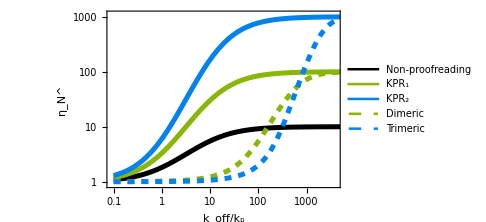

```mathematica
clist={categoricalcmap[[1]],categoricalcmap[[4]],categoricalcmap[[6]]};
fig2params={Rt->10^3,c->10^-3,kon->1,kf->10^-3};
fig2paramsAlt={c->10^-3,kon->1,kf->10^-1};

Fig2A=LogLogPlot[{
Evaluate[Evaluate[η0/.{koff->g kf}]/.fig2params/.δ->0.1],
Evaluate[Evaluate[η1/.{koff->g kf}]/.fig2params/.δ->0.1],
Evaluate[Evaluate[η2/.{koff->g kf}]/.fig2params/.δ->0.1],
Evaluate[HomoDimer[c,Rt,δ koff/kon ,δ koff/kf ]/HomoDimer[c,Rt,koff/kon,koff/kf]/.{koff->g kf}/.fig2params/.δ->0.1],
Evaluate[Tri[c,Rt,δ koff/kon ,δ koff/kf,δ koff/kf ]/Tri[c,Rt,koff/kon,koff/kf,koff/kf]/.{koff->g kf}/.fig2params/.δ->0.1]},
{g,10^-1,4*10^4},
Frame->{{True,False},{True,False}},FrameStyle->Black,FrameLabel->{"k_off/k_p","η_N^"},PlotLegends->{"Non-proofreading","KPR_1","KPR_2","Dimeric","Trimeric"},
ImageSize->Medium,LabelStyle-> {Black,FontSize->16},PlotStyle->Join[Table[{clist[[i]],Thickness[0.01]},{i,1,3}],Table[{clist[[i]],Thickness[0.01],Dashed},{i,2,3}]],
FrameTicks->{{Table[{10^i,Superscript[10,i]},{i,0,3}],None},{Table[{10^i,Superscript[10,i]},{i,-2,4}],None}},TicksStyle->Black,PlotRange->{{0.9*10^-1,4*10^3},{0.9,1.1*10^3}}]
```

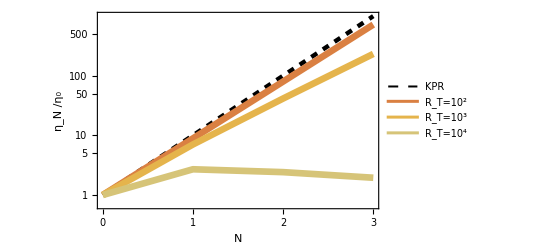

```mathematica
clist=Table[ColorData["BeachColors",i/(5-1)],{i,0,5-1}];

KOFF=1;
KON=1;
KF=10^-4;
RT=10^3;
δK=0.1;
CTEST=0.01;
testparams={kf->KF,koff->KOFF,kon->KON,c->CTEST,δ->0.1,Rt->RT};


ηREF=η0/.testparams;
KPRscaling={{0,η0/η0},{1,η1/η0},{2,η2/η0},{3,η3/η0}}/.testparams;
MultimerScaling={{0,1},{1,1/ηREF HomoDimer[CTEST,RT,δK KOFF/KON,δK KOFF/KF]/HomoDimer[CTEST,RT,KOFF/KON,KOFF/KF]},{2,1/ηREF Tri[CTEST,RT,δK KOFF/KON,δK KOFF/KF,δK KOFF/KF]/Tri[CTEST,RT,KOFF/KON,KOFF/KF,KOFF/KF]},{3,1/ηREF TetAct[CTEST,RT,δK KOFF/KON,δK KOFF/KF,δK KOFF/KF,δK KOFF/KF]/TetAct[CTEST,RT,KOFF/KON,KOFF/KF,KOFF/KF,KOFF/KF]}};

MultimerScalingReducedRt={{0,1},{1,1/ηREF HomoDimer[CTEST,0.1RT,δK KOFF/KON,δK KOFF/KF]/HomoDimer[CTEST,0.1RT,KOFF/KON,KOFF/KF]},{2,1/ηREF Tri[CTEST,0.1RT,δK KOFF/KON,δK KOFF/KF,δK KOFF/KF]/Tri[CTEST,0.1RT,KOFF/KON,KOFF/KF,KOFF/KF]},{3,1/ηREF TetAct[CTEST,0.1RT,δK KOFF/KON,δK KOFF/KF,δK KOFF/KF,δK KOFF/KF]/TetAct[CTEST,0.1RT,KOFF/KON,KOFF/KF,KOFF/KF,KOFF/KF]}};
MultimerScalingIncreasedRt={{0,1},{1,1/ηREF HomoDimer[CTEST,10RT,δK KOFF/KON,δK KOFF/KF]/HomoDimer[CTEST,10RT,KOFF/KON,KOFF/KF]},{2,1/ηREF Tri[CTEST,10RT,δK KOFF/KON,δK KOFF/KF,δK KOFF/KF]/Tri[CTEST,10RT,KOFF/KON,KOFF/KF,KOFF/KF]},{3,1/ηREF TetAct[CTEST,10RT,δK KOFF/KON,δK KOFF/KF,δK KOFF/KF,δK KOFF/KF]/TetAct[CTEST,10RT,KOFF/KON,KOFF/KF,KOFF/KF,KOFF/KF]}};


Fig2B=ListLogPlot[{KPRscaling,MultimerScalingReducedRt,MultimerScaling,MultimerScalingIncreasedRt},
PlotStyle->Join[{{Black,Thickness[0.008],Dashed}},Table[{clist[[i]],Thickness[0.012]},{i,1,3}]],LabelStyle-> {Black,FontSize->16},
Joined->True,PlotLegends->{"KPR","R_T=10^2","R_T=10^3","R_T=10^4"},Frame->{{True,False},{True,False}},FrameLabel->{"N","η_N /η_0"},FrameStyle->Black,FrameTicks->{{0,1,2,3},Automatic}]
```

### Figure 3 (Free energy landscapes)

S=k_B Log[Ω]  and Ω=Σ_i(A/a_0)^R_i/(R_i!) in the dilute limit.
Using Stirling’s approximation, Log(x!)=x(Log[x]-1), this becomes

S=k_B Σ_i(R_i Log[A/a_0]-R_i Log[R_i]+R_i)
S=-k_BΣ_i(R_i Log[a_0 R_i/A]-R_i)

```mathematica
DimerChemEq={kon c R0==koff R1,
		      kf R0 R1==koff R2};
DimerF=ϵ1 R1 A+ϵ2 R2 A-μ (R1+R2)A-kT (R1 Log[R1/A a0])
```

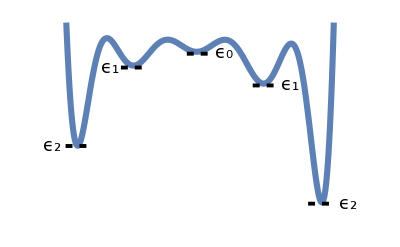

```mathematica
welldepths=Join[
Table[{-Ns,-Log[(0.2koff)/kon((0.2koff)/kf)^Ns 1/((Ns+1)!)]}/.{kon->1,koff->1,kf->0.01},{Ns,3,1,-1}],
Table[{Ns,-Log[koff/kon(koff/kf)^Ns 1/((Ns+1)!)]}/.{kon->1,koff->1,kf->0.01},{Ns,0,3}]
];
wellheights=Table[{i,welldepths[[i+3.5,2]]+2},{i,-2.5,2.5}];
landscape1=Riffle[welldepths,wellheights];
landscape1[[6,2]]=0.9landscape1[[8,2]];


Fig3A=Plot[{
Interpolation[landscape1,InterpolationOrder->12][Rx],
Piecewise[{{-0.4,Abs[Rx]<0.25}},None],
Piecewise[{{-5.9,Abs[Rx-1.25]<0.25}},None],
Piecewise[{{-2.8,Abs[Rx+1.25]<0.25}},None],
Piecewise[{{-26.4,Abs[Rx-2.3]<0.25}},None],
Piecewise[{{-16.4,Abs[Rx+2.3]<0.25}},None]},
{Rx,-2.6,2.6},

Axes->False,
PlotStyle->Join[{{cmap[[1]],Thickness[0.011]}},Table[{Black,Dashed,Thickness[0.007]},{i,1,5}]],
PlotRange->{{-3.1,3.1},{-30,5}},

Epilog->{
Text[Style["ϵ_0",FontSize->18],{0.45,-0.25}],
Text[Style["ϵ_1",FontSize->18],{1.7,-5.9}],
Text[Style["ϵ_2",FontSize->18],{2.8,-26.4}],
Text[Style["ϵ_1",FontSize->18],{-1.7,-2.8}],
Text[Style["ϵ_2",FontSize->18],{-2.8,-16.4}]}]
```

```mathematica
(* Figure 3B was made in Inkscape. *)
```

### Figure 4 (SNR)

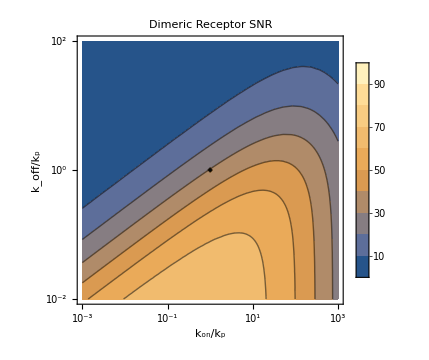
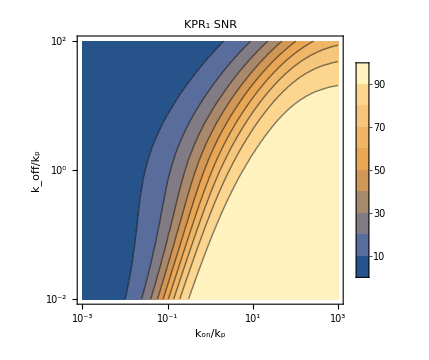

```mathematica
gxTicks={{Table[{i,Superscript[10,i]},{i,-4,2,2}],None},{Table[{i,Superscript[10,i]},{i,-3,3,2}],None}};
gxParams1={kon->1,koff->10^gtest,c->10^ctest,kf->1,kp->1,t->100,Rt->100};
gxParams2={kon->1,koff->10^gtest,c->10^ctest,kf->100,kp->1,t->100,Rt->100};
Fig4A=
ContourPlot[65 ⅇ^(1/2 (-ctest (100000 ctest)-gtest (100000gtest)))+μDi/(√ΣDi)/.gxParams1,{ctest,-3,3},{gtest,-2,2},FrameLabel->{"k_on/k_p","k_off/k_p"},PlotLegends->Automatic,PlotLabel->"Dimeric Receptor\n SNR",LabelStyle->{Black,FontSize->24},TicksStyle->{Black,FontSize->24},FrameTicks->gxTicks,ImageSize->Medium,PerformanceGoal->"Quality",WorkingPrecision->20,PlotRange->{0,100}];

Fig4B=ContourPlot[√Rt μ1/(√Σ1)/.gxParams2,{ctest,-3,3},{gtest,-2,2},FrameLabel->{"k_on/k_p","k_off/k_p"},PlotLegends->Automatic,PlotLabel->"KPR_1 SNR",LabelStyle->{Black,FontSize->24},TicksStyle->{Black,FontSize->24},FrameTicks->gxTicks,ImageSize->Medium];
Row[{Fig4A,Fig4B}]

(* Added extra term just to force the scales to match between the two graphs *)
```

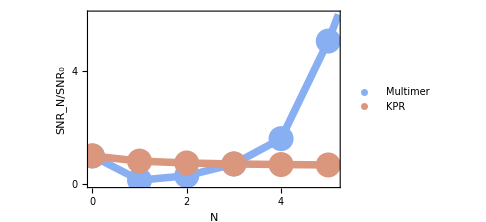

```mathematica
gxTicks={{Table[{i,Superscript[10,i]},{i,-2,2}],None},{Table[{i,Superscript[10,i]},{i,-3,3,2}],None}};
KOFF=100;(*koff=100 means koff/(kf Rt/A)=1*)(**)
CPARAM=10^-1;
MultimerParams={kon->1,koff->KOFF,c->CPARAM,kf->1,kp->1,t->100};
KPRparams={kon->1,koff->KOFF,c->CPARAM,kp->1,t->100};

SNRvN={{0,1},{1,(μDi/(√ΣDi))/(√Rt μ0/(√Σ0))/.Rt->200},{2,(μTri/(√ΣTri))/(√Rt μ0/(√Σ0))/.Rt->300},{3,(μTet/(√ΣTet))/(√Rt μ0/(√Σ0))/.Rt->400},{4,MultSNR[Mult4[1,CPARAM,KOFF,1,500],1,100,4]/(√Rt μ0/(√Σ0)/.Rt->500)},{5,MultSNR[Mult5[1,CPARAM,KOFF,1,600],1,100,5]/(√Rt μ0/(√Σ0)/.Rt->600)},{6,MultSNR[Mult6[1,CPARAM,KOFF,1,700],1,100,6]/(√Rt μ0/(√Σ0)/.Rt->700)}}/.MultimerParams//N;
SNRkprvN={{0,1},{1,(μ1/(√Σ1))/(μ0/(√Σ0))/.kf->200},{2,(μ2/(√Σ2))/(μ0/(√Σ0))/.kf->300},{3,(μ3/(√Σ3))/(μ0/(√Σ0))/.kf->400},{4,(μ4/(√Σ4))/(μ0/(√Σ0))/.kf->500},{5,(μN/(√ΣN))/(μ0/(√Σ0))/.expandParams/.kf->600/.Ns->5},{6,(μN/(√ΣN))/(μ0/(√Σ0))/.expandParams/.kf->700/.Ns->6}}/.KPRparams//N;
Fig4C=
Legended[
Show[
ListPlot[{SNRvN,SNRkprvN},Joined->True,PlotStyle->{{bigrad[[3]],Thickness[0.015]},{bigrad[[7]],Thickness[0.015]}},ImageSize->Medium,Frame->{{True,False},{True,False}},FrameLabel->{"N","SNR_N/SNR_0"},FrameTicks->{Table[i,{i,0,6}],Table[i,{i,0,10,2}]},TicksStyle->{Black,FontSize->24},LabelStyle->{Black,FontSize->24},PlotRange->{{Automatic,5.15},{Automatic,6}}],
ListPlot[{SNRvN,SNRkprvN},PlotStyle->{{bigrad[[3]],PointSize[0.05]},{bigrad[[7]],PointSize[0.05]}},ImageSize->Medium]
],
PointLegend[{bigrad[[3]],bigrad[[7]]},{"Multimer","KPR"},LegendFunction->"Frame",LegendMarkerSize->30]
]
```

### Figure 5 (Absolute discrimination)

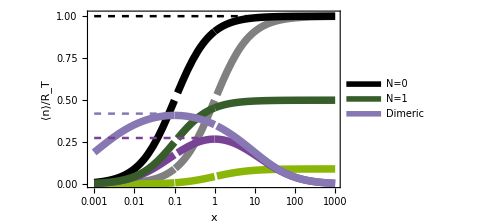

```mathematica
ClearAll[CTEST];
testParams={kon->1,kp->1,t->100,c->CTEST ,koff->1,kf->0.1,Rt->50,δ->0.1};
clist={categoricalcmap[[4]],ColorData[8,"ColorList"][[7]],cmap[[5]],categoricalcmap[[8]]};
plotoptions={
Frame->{{True,False},{True,False}},FrameStyle->Black,FrameLabel->{"x","⟨n⟩/R_T"},
PlotLegends->{None,None,None,"N=0","N=1","Dimeric"},
ImageSize->Medium,LabelStyle-> {Black,FontSize->16},

PlotStyle->{
{Gray,Thickness[0.015]},
{clist[[1]],Thickness[0.015]},
{clist[[4]],Thickness[0.015]},
{Black,Thickness[0.015]},
{clist[[2]],Thickness[0.015]},
{clist[[3]],Thickness[0.015]},
{Black,Dashed,Thickness[0.005]},
{clist[[3]],Dashed,Thickness[0.005]},
{clist[[4]],Dashed,Thickness[0.005]}},

FrameTicks->{{Automatic,None},{Table[{10^i,Superscript[10,i]},{i,-3,3}],None}},TicksStyle->Black,PlotRange->{{0.0009,1010},{0.000000001,1.01}}};
expression=#/.testParams&/@{μ0/(kp t),μ1/(kp t),μDi/(kp t Rt),Evaluate[μ0/(kp t)/.koff->δ koff],Evaluate[μ1/(kp t)/.koff->δ koff],Evaluate[μDi/(kp t Rt)/.koff->δ koff]};
expression=Join[Evaluate@expression,{1,0.42*HeavisideTheta[0.1-CTEST],0.275*HeavisideTheta[1-CTEST]}];

Fig5A=LogLinearPlot[Evaluate@expression,{CTEST,0.001,1000},Evaluate@plotoptions]
```

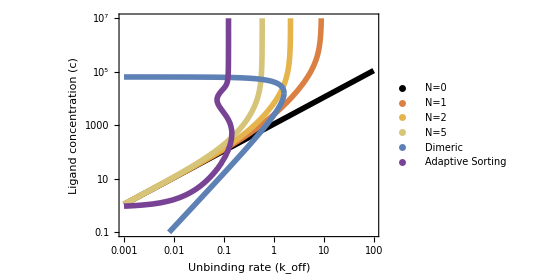

```mathematica
p1={kon->10^-4,kp->1,t->300,Nx->30,kf->1};
p2={kon->10^-4,kp->1,t->300,Ny->3000,kf->0.01,Rt->100};

c0=Solve[μ0== Nx,c][[1]];
c1=Solve[μ1== Nx,c][[1]];
c2=Solve[μ2== Nx,c][[1]];
c5=Solve[Evaluate[μN/.Ns->5]== Nx,c][[1]];
cDim=Solve[μDi==Ny,c];

ls=c/.{c0/.p1,c1/.p1,c2/.p1,c5/.p1,cDim/.p2};

KPRcolors=Table[ColorData["BeachColors",i/(5-1)],{i,0,5-1}];
AScolors=categoricalcmap[[8]];
Dimercolors=ColorData[97,"ColorList"][[1]];

Fig5B=Legended[
Show[
LogLogPlot[ls,{koff,10^-3,10^2},AspectRatio->0.7,PlotRange->{{0.001,100},{0.1,10^7}},PlotStyle->Join[{{Black,Thickness[0.01]}},Table[{KPRcolors[[i]],Thickness[0.01]},{i,1,3}],{{Dimercolors,Thickness[0.01]},{Dimercolors,Thickness[0.01]}}],
Frame->{{True,False},{True,False}},FrameLabel->{"Unbinding rate (k_off)","Ligand concentration (c)"},TicksStyle->Black,LabelStyle->{Black,FontSize->18},FrameTicks->{{Table[{10^i,Superscript[10,i-4]},{i,-6,6,2}],None},{Table[{10^i,Superscript[10,i]},{i,-3,4}],None}}],

ListLogLogPlot[Evaluate[{10^#[[1]],10^#[[2]]}&/@points[[6]]],AspectRatio->0.7,Joined->True,PlotStyle->{AScolors,Thickness[0.01]}]
],
PointLegend[Join[{{Black,Thickness[0.01]}},Table[KPRcolors[[i]],{i,1,3}],{White,Dimercolors,AScolors}],
{"N=0","N=1","N=2","N=5","","Dimeric","Adaptive Sorting"},LegendMarkerSize->25,LegendLayout->{"Column",2}]
]
```

### Figure S1(Gillespie simulations to validate expression of dimeric variance)

```mathematica
simparams={NA->6.022*10^23,volEC->10^-5,kon->3.321*10^-14,koff->1,kf->3.623*10^-4,kr->1,kp->10^-6,Rt->4000,t->10^4};
```

```mathematica
dat=Import["C:\\Users\\Duncan\\OneDrive - University of Toronto\\Documents\\University\\Grad Studies Year 6\\KPR Project\\KPR_Multimer_Manuscript\\Figures\\Raw PDFs\\Gillespie-validation.csv","Data"];
doses=Table[dat[[i,1]],{i,2,Length[dat]}];
meanN=Table[dat[[i,2]],{i,2,Length[dat]}];
sigN=Table[dat[[i,3]],{i,2,Length[dat]}];
meanR=Table[dat[[i,4]],{i,2,Length[dat]}];
sigR=Table[dat[[i,5]],{i,2,Length[dat]}];
meanNtheory=Table[dat[[i,6]],{i,2,Length[dat]}];
sigNtheory=Table[dat[[i,7]],{i,2,Length[dat]}];
meanRtheory=Table[dat[[i,8]],{i,2,Length[dat]}];
sigRtheory=Table[dat[[i,9]],{i,2,Length[dat]}];
```

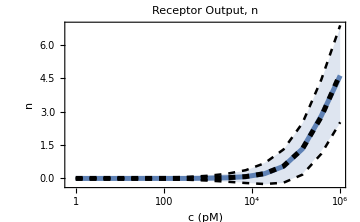
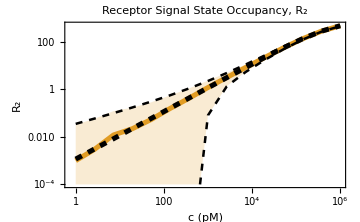

```mathematica
FigS1=Row[{
ListLogLinearPlot[
{Table[{doses[[i]],meanN[[i]]},{i,1,Length[doses]}],
Table[{doses[[i]],meanN[[i]]+sigN[[i]]},{i,1,Length[doses]}],
Table[{doses[[i]],meanN[[i]]-sigN[[i]]},{i,1,Length[doses]}],
Table[{doses[[i]],meanNtheory[[i]]},{i,1,Length[doses]}],
Table[{doses[[i]],meanNtheory[[i]]+sigNtheory[[i]]},{i,1,Length[doses]}],
Table[{doses[[i]],meanNtheory[[i]]-sigNtheory[[i]]},{i,1,Length[doses]}]
},
Joined->True,PlotStyle->{{cmap[[1]],Thickness[0.01]},None,None,{Black,Dashed,Thickness[0.01]},{Black,Dashed,Thickness[0.005]},{Black,Dashed,Thickness[0.005]}},
Filling->{1->{2},1->{3}},
PlotRange->All,PlotLabel->"Receptor Output, n",FrameLabel->{"c (pM)","n"},
Frame->{{True,False},{True,False}},LabelStyle->{Black,FontSize->16},TicksStyle->Black,ImageSize->Medium],

ListLogLogPlot[{
Table[{doses[[i]],meanR[[i]]},{i,1,Length[doses]}],
Table[{doses[[i]],meanR[[i]]+sigR[[i]]},{i,1,Length[doses]}],
Table[{doses[[i]],Max[10^-8,meanR[[i]]-sigR[[i]]]},{i,1,Length[doses]}],
Table[{doses[[i]],meanRtheory[[i]]},{i,1,Length[doses]}],
Table[{doses[[i]],meanRtheory[[i]]+sigRtheory[[i]]},{i,1,Length[doses]}],
Table[{doses[[i]],Max[10^-8,meanRtheory[[i]]-sigRtheory[[i]]]},{i,1,Length[doses]}]},
Joined->True,PlotStyle->{{cmap[[2]],Thickness[0.01]},None,None,{Black,Dashed,Thickness[0.01]},{Black,Dashed,Thickness[0.005]},{Black,Dashed,Thickness[0.005]}},
Filling->{1->{2},1->{3}},
PlotRange->{All,{10^-4,Automatic}},PlotLabel->"Receptor Signal State Occupancy, R_2",FrameLabel->{"c (pM)","R_2"},
Frame->{{True,False},{True,False}},LabelStyle->{Black,FontSize->16},TicksStyle->Black,ImageSize->Medium]
}]
```

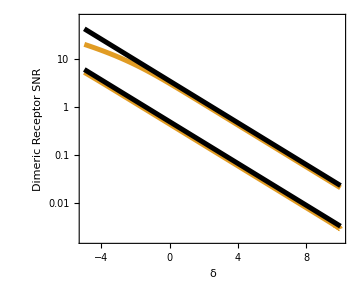

```mathematica
FigS1C=LogPlot[{
SNRDimerNonEq/.p1,0.5(E)^(-δTEST/2),
SNRDimerNonEq/.p2,3.5(E)^(-δTEST/2)},{δTEST,-5,10},
Frame->{{True,False},{True,False}},FrameLabel->{"δ","Dimeric Receptor SNR"},FrameStyle->Black,LabelStyle->{Black,FontSize->24},ImageSize->Medium,AspectRatio->0.8,FrameTicks->{Automatic,{100,10,1,0.1,0.01,0.001}},PlotStyle->{{cmap[[2]],Thickness[0.01]},{Black,Thickness[0.01]},{cmap[[2]],Thickness[0.01]},{Black,Thickness[0.01]}}]
```

### Figure S2 (More details on the reversible KPR model)

```mathematica
ηthermo=((PssKPR1[[3]]/.{koff->δ koff})/PssKPR1[[3]]//FullSimplify)/.{kf->koff/g,c ν->KONC/r0}//FullSimplify;
```

```mathematica
figS2params={Rt->10^2,c->10^-9,kon->1,koff->10^-6,kf->10^-9};
FigS2B=LogLogPlot[{
Evaluate[Evaluate[η0/.{koff->g kf}]/.figS2params/.δ->0.1],
Evaluate[Evaluate[ηthermo/.{koff->g kf,r0->1,ν->1,δ02->2,δ21->0,KONC->10^-9}]/.figS2params/.δ->0.1],
Evaluate[Evaluate[η1/.{koff->g kf}]/.figS2params/.δ->0.1],
Evaluate[HomoDimer[c,Rt,δ(g kf)/kon ,δ g ]/HomoDimer[c,Rt,(g kf)/kon,g]/.figS2params/.δ->0.1]},
{g,10^-2,10^4},
Frame->{{True,False},{True,False}},FrameStyle->Black,FrameLabel->{"Proofreading strength g","η"},PlotLegends->{"Non-proofreading","Reversible KPR_1","Irreversible KPR_1","Dimeric"},
ImageSize->Medium,LabelStyle-> {Black,FontSize->16},PlotStyle->{{contourcmap[[1]],Thickness[0.01]},{contourcmap[[1]],Thickness[0.01],Dashed},{contourcmap[[3]],Thickness[0.01]},{contourcmap[[3]],Thickness[0.01],Dashed}},
FrameTicks->{{Table[{10^i,Superscript[10,i]},{i,0,3}],None},{Table[{10^i,Superscript[10,i]},{i,-2,4}],None}},TicksStyle->Black,PlotRange->{{0.9*10^-2,10^4},{0.9*10^0,1.1*10^2}},AspectRatio->.75];
```

```mathematica
ATP=30 kT;
δMIN=-1;
δMAX=15;
GMIN=-1;
GMAX=5;
testParams={r0->1,ν->1,koff->0.01*10^GTEST,kf->0.01,c->1,δ02->δTEST,δ21->0,δ->0.1,kon->1,KONC->1};
xgFrameTicks={{Table[{i,Superscript[10,i]},{i,GMIN,GMAX,2}],None},{Automatic,None}};
plotoptions={FrameLabel->{"δ_02  (kT)","K_D"},FrameTicks->xgFrameTicks,FrameStyle->Black,LabelStyle->{Black,FontSize->24},PlotLegends->Placed[Automatic,Right],AspectRatio->1,ImageSize->Medium};
```

```mathematica
FigS2C=LogLogPlot[{
Evaluate[η0/.figS2params],
Evaluate[Evaluate[ηthermo/.g->koff/kf/.{r0->1,ν->1,δ02->2,δ21->0,KONC->10^-9}]/.figS2params],
Evaluate[η1/.figS2params],
Evaluate[HomoDimer[c,Rt,δ koff/kon,δ koff/kf]/HomoDimer[c,Rt,koff/kon,koff/kf]/.figS2params]},

{δ,10^-3,1},
Frame->{{True,False},{True,False}},FrameStyle->Black,
(*PlotLegends->{"Non-proofreading","Reversible KPR_1","Irreversible KPR_1","Dimeric"},*)
FrameLabel->{"Relative binding strength ζ","η"},
ImageSize->Medium,LabelStyle-> {Black,FontSize->16},PlotStyle->{{contourcmap[[1]],Thickness[0.01]},{contourcmap[[1]],Thickness[0.01],Dashed},{contourcmap[[3]],Thickness[0.01]},{contourcmap[[3]],Thickness[0.01],Dashed}},
TicksStyle->Black,
FrameTicks->{{Table[{10^i,Superscript[10,i]},{i,0,9,2}],None},{Table[{10^i,Superscript[10,i]},{i,-3,0}],None}},PlotRange->{{10^-3,1},{1,10^9}},AspectRatio->.75];
```

```mathematica
FigS2=Column[{Row[{FigS2B,FigS2C}]}]
```

```mathematica
p1test={kp->1,t->100,kon->1,c->0.001,RT->1000,koff->1,kf->0.01,δ21->Log[2]};
SNRDimerNonEq/.p1test
koff E^δ21/(kf RT)/.p1test
```

2.22245

0.2

```mathematica
p1test={kp->1,t->100,kon->1,c->0.001,RT->1000,koff->1,kf->0.005,δ21->0};
SNRDimerNonEq/.p1test
koff E^δ21/(kf RT)/.p1test
```

2.22245

0.2

```mathematica
p1test={kp->1,t->100,kon->1,c->0.001,RT->1000,koff->1,kf->0.001,δ21->0};
SNRDimerNonEq/.p1test
koff E^δ21/(kf RT)/.p1test

p1test={kp->1,t->100,kon->1,c->0.001,RT->1000,koff->1,kf->0.01,δ21->Log[10]};
SNRDimerNonEq/.p1test
koff E^δ21/(kf RT)/.p1test
```

0.994024

1.

0.994024

1.

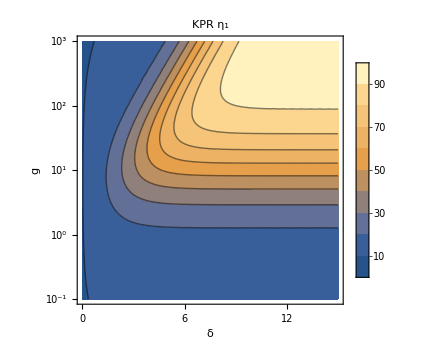

```mathematica
FigEntropyB=ContourPlot[R2KPR1[c,kon,ζ koff,kf,δ21,δ02,RT]/R2KPR1[c,kon,koff,kf,δ21,δ02,RT]/.{kon->1,c->0.001,koff->1,ζ->0.1,RT->100,δ21->δ,δ02->δ}/.{δ->δtest,kf->10^-gtest},{δtest,0,15},{gtest,-1,3},
FrameLabel->{"δ","g"},PlotLegends->Automatic,PlotLabel->"KPR η_1",LabelStyle->{Black,FontSize->24},TicksStyle->{Black,FontSize->24},ImageSize->Medium,FrameTicks->{{Table[{i,Superscript[10,i]},{i,-1,3}],None},{Table[i,{i,0,15,3}],None}}]
```

### Figure S3 (Other parameter regimes for SNR scaling)

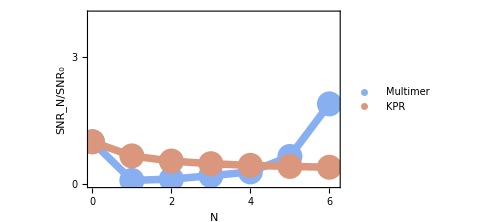

```mathematica
gxTicks={{Table[{i,Superscript[10,i]},{i,-2,2}],None},{Table[{i,Superscript[10,i]},{i,-3,3,2}],None}};
KOFF=250;(*koff=100 means koff/(kf Rt/A)=1*)(**)
CPARAM=10^-1;
MultimerParams={kon->1,koff->KOFF,c->CPARAM,kf->1,kp->1,t->100};
KPRparams={kon->1,koff->KOFF,c->CPARAM,kp->1,t->100};

SNRvN={{0,1},{1,(μDi/(√ΣDi))/(√Rt μ0/(√Σ0))/.Rt->200},{2,(μTri/(√ΣTri))/(√Rt μ0/(√Σ0))/.Rt->300},{3,(μTet/(√ΣTet))/(√Rt μ0/(√Σ0))/.Rt->400},{4,MultSNR[Mult4[1,CPARAM,KOFF,1,500],1,100,4]/(√Rt μ0/(√Σ0)/.Rt->500)},{5,MultSNR[Mult5[1,CPARAM,KOFF,1,600],1,100,5]/(√Rt μ0/(√Σ0)/.Rt->600)},{6,MultSNR[Mult6[1,CPARAM,KOFF,1,700],1,100,6]/(√Rt μ0/(√Σ0)/.Rt->700)}}/.MultimerParams//N;
SNRkprvN={{0,1},{1,(μ1/(√Σ1))/(μ0/(√Σ0))/.kf->200},{2,(μ2/(√Σ2))/(μ0/(√Σ0))/.kf->300},{3,(μ3/(√Σ3))/(μ0/(√Σ0))/.kf->400},{4,(μ4/(√Σ4))/(μ0/(√Σ0))/.kf->500},{5,(μN/(√ΣN))/(μ0/(√Σ0))/.expandParams/.kf->600/.Ns->5},{6,(μN/(√ΣN))/(μ0/(√Σ0))/.expandParams/.kf->700/.Ns->6}}/.KPRparams//N;
FigS5A=
Legended[
Show[
ListPlot[{SNRvN,SNRkprvN},Joined->True,PlotStyle->{{bigrad[[3]],Thickness[0.015]},{bigrad[[7]],Thickness[0.015]}},ImageSize->Medium,Frame->{{True,False},{True,False}},FrameLabel->{"N","SNR_N/SNR_0"},FrameTicks->{Table[i,{i,0,6}],Table[i,{i,0,10,1}]},TicksStyle->{Black,FontSize->24},LabelStyle->{Black,FontSize->24},PlotRange->{{Automatic,6.15},{Automatic,4}}],
ListPlot[{SNRvN,SNRkprvN},PlotStyle->{{bigrad[[3]],PointSize[0.05]},{bigrad[[7]],PointSize[0.05]}},ImageSize->Medium]
],
PointLegend[{bigrad[[3]],bigrad[[7]]},{"Multimer","KPR"},LegendFunction->"Frame",LegendMarkerSize->30]
]
```

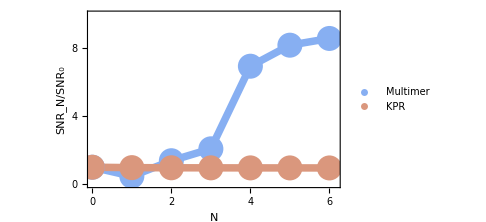

```mathematica
gxTicks={{Table[{i,Superscript[10,i]},{i,-2,2}],None},{Table[{i,Superscript[10,i]},{i,-3,3,2}],None}};
KOFF=10;(*koff=100 means koff/(kf Rt/A)=1*)(**)
CPARAM=10^-1;
MultimerParams={kon->1,koff->KOFF,c->CPARAM,kf->1,kp->1,t->100};
KPRparams={kon->1,koff->KOFF,c->CPARAM,kp->1,t->100};

SNRvN={{0,1},{1,(μDi/(√ΣDi))/(√Rt μ0/(√Σ0))/.Rt->200},{2,(μTri/(√ΣTri))/(√Rt μ0/(√Σ0))/.Rt->300},{3,(μTet/(√ΣTet))/(√Rt μ0/(√Σ0))/.Rt->400},{4,MultSNR[Mult4[1,CPARAM,KOFF,1,500],1,100,4]/(√Rt μ0/(√Σ0)/.Rt->500)},{5,MultSNR[Mult5[1,CPARAM,KOFF,1,600],1,100,5]/(√Rt μ0/(√Σ0)/.Rt->600)},{6,MultSNR[Mult6[1,CPARAM,KOFF,1,700],1,100,6]/(√Rt μ0/(√Σ0)/.Rt->700)}}/.MultimerParams//N;
SNRkprvN={{0,1},{1,(μ1/(√Σ1))/(μ0/(√Σ0))/.kf->200},{2,(μ2/(√Σ2))/(μ0/(√Σ0))/.kf->300},{3,(μ3/(√Σ3))/(μ0/(√Σ0))/.kf->400},{4,(μ4/(√Σ4))/(μ0/(√Σ0))/.kf->500},{5,(μN/(√ΣN))/(μ0/(√Σ0))/.expandParams/.kf->600/.Ns->5},{6,(μN/(√ΣN))/(μ0/(√Σ0))/.expandParams/.kf->700/.Ns->6}}/.KPRparams//N;
FigS5B=
Legended[
Show[
ListPlot[{SNRvN,SNRkprvN},Joined->True,PlotStyle->{{bigrad[[3]],Thickness[0.015]},{bigrad[[7]],Thickness[0.015]}},ImageSize->Medium,Frame->{{True,False},{True,False}},FrameLabel->{"N","SNR_N/SNR_0"},FrameTicks->{Table[i,{i,0,6}],Table[i,{i,0,10,2}]},TicksStyle->{Black,FontSize->24},LabelStyle->{Black,FontSize->24},PlotRange->{{Automatic,6.15},{Automatic,10}}],
ListPlot[{SNRvN,SNRkprvN},PlotStyle->{{bigrad[[3]],PointSize[0.05]},{bigrad[[7]],PointSize[0.05]}},ImageSize->Medium]
],
PointLegend[{bigrad[[3]],bigrad[[7]]},{"Multimer","KPR"},LegendFunction->"Frame",LegendMarkerSize->30]
]
```

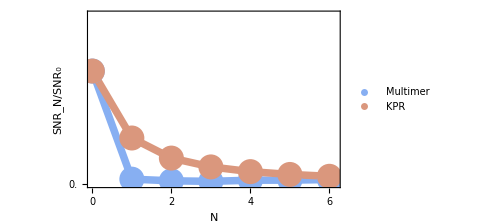

```mathematica
gxTicks={{Table[{i,Superscript[10,i]},{i,-2,2}],None},{Table[{i,Superscript[10,i]},{i,-3,3,2}],None}};
KOFF=1000;(*koff=100 means koff/(kf Rt/A)=1*)
CPARAM=10^-1;
MultimerParams={kon->1,koff->KOFF,c->CPARAM,kf->1,kp->1,t->100};
KPRparams={kon->1,koff->KOFF,c->CPARAM,kp->1,t->100};

SNRvN={{0,1},{1,(μDi/(√ΣDi))/(√Rt μ0/(√Σ0))/.Rt->200},{2,(μTri/(√ΣTri))/(√Rt μ0/(√Σ0))/.Rt->300},{3,(μTet/(√ΣTet))/(√Rt μ0/(√Σ0))/.Rt->400},{4,MultSNR[Mult4[1,CPARAM,KOFF,1,500],1,100,4]/(√Rt μ0/(√Σ0)/.Rt->500)},{5,MultSNR[Mult5[1,CPARAM,KOFF,1,600],1,100,5]/(√Rt μ0/(√Σ0)/.Rt->600)},{6,MultSNR[Mult6[1,CPARAM,KOFF,1,700],1,100,6]/(√Rt μ0/(√Σ0)/.Rt->700)}}/.MultimerParams//N;
SNRkprvN={{0,1},{1,(μ1/(√Σ1))/(μ0/(√Σ0))/.kf->200},{2,(μ2/(√Σ2))/(μ0/(√Σ0))/.kf->300},{3,(μ3/(√Σ3))/(μ0/(√Σ0))/.kf->400},{4,(μ4/(√Σ4))/(μ0/(√Σ0))/.kf->500},{5,(μN/(√ΣN))/(μ0/(√Σ0))/.expandParams/.kf->600/.Ns->5},{6,(μN/(√ΣN))/(μ0/(√Σ0))/.expandParams/.kf->700/.Ns->6}}/.KPRparams//N;
FigS5C=
Legended[
Show[
ListPlot[{SNRvN,SNRkprvN},Joined->True,PlotStyle->{{bigrad[[3]],Thickness[0.015]},{bigrad[[7]],Thickness[0.015]}},ImageSize->Medium,Frame->{{True,False},{True,False}},FrameLabel->{"N","SNR_N/SNR_0"},FrameTicks->{Table[i,{i,0,6}],Table[i,{i,0,14,0.5}]},TicksStyle->{Black,FontSize->24},LabelStyle->{Black,FontSize->24},PlotRange->{{Automatic,6.15},{Automatic,1.5}}],
ListPlot[{SNRvN,SNRkprvN},PlotStyle->{{bigrad[[3]],PointSize[0.05]},{bigrad[[7]],PointSize[0.05]}},ImageSize->Medium]
],
PointLegend[{bigrad[[3]],bigrad[[7]]},{"Multimer","KPR"},LegendFunction->"Frame",LegendMarkerSize->30]
]
```

### Figure S4 (Antagonism)

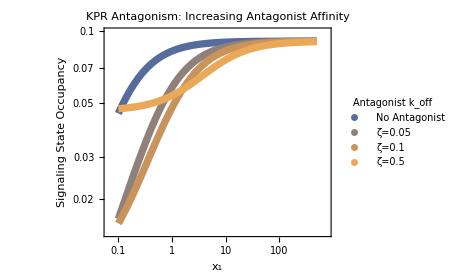

```mathematica
p={kon->1,koff1->0.1,kf->0.01};
pops={PlotStyle->Evaluate[{Thickness[0.015],#}&/@contourcmap],
Frame->{{True,False},{True,False}},FrameLabel->{"x_1","Signaling State Occupancy"},AspectRatio->0.8,ImageSize->350,TicksStyle->Black,LabelStyle-> {Black,FontSize->20},Axes->{True,False}};
leg=PointLegend[Table[contourcmap[[i]],{i,1,6}],{"No Antagonist","ζ=0.05","ζ=0.1","ζ=0.5"},LegendMarkerSize->25,LegendLabel->"Antagonist k_off",LabelStyle->{Directive[FontSize->20]}];

μmixedKPR=mixedKPR[[3]]+mixedKPR[[5]];

FigS4A=Legended[
LogLogPlot[{μmixedKPR/.p/.{c2->0,koff2->2},
μmixedKPR/.p/.{c2->10,koff2->2},
μmixedKPR/.p/.{c2->10,koff2->1},
μmixedKPR/.p/.{c2->10,koff2->0.2}},{c1,0.1,500},PlotLabel->"KPR Antagonism:\nIncreasing Antagonist Affinity",Evaluate@pops],
leg]
```

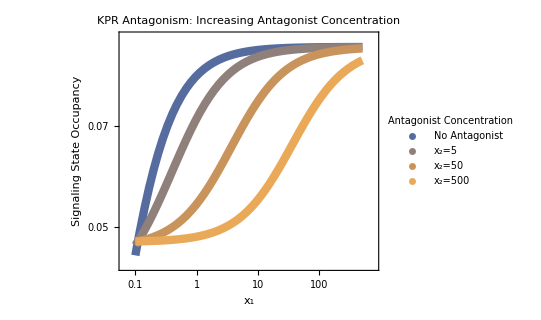

```mathematica
p={kon->1,koff1->0.1,kf->0.01};
pops={PlotStyle->Evaluate[{Thickness[0.015],#}&/@contourcmap],
Frame->{{True,False},{True,False}},FrameLabel->{"x_1","Signaling State Occupancy"},AspectRatio->0.8,ImageSize->400,TicksStyle->Black,LabelStyle-> {Black,FontSize->20},Axes->{True,False}};
leg=PointLegend[Table[contourcmap[[i]],{i,1,6}],{"No Antagonist","x_2=5","x_2=50","x_2=500"},LegendMarkerSize->25,LegendLabel->"Antagonist Concentration",LabelStyle->{Directive[FontSize->20]}];

μmixedKPR=mixedKPR[[3]]+mixedKPR[[5]];

AntagKOFF=0.2;
FigS4B=Legended[
LogLogPlot[{μmixedKPR/.p/.{c2->0,koff2->AntagKOFF},
μmixedKPR/.p/.{c2->1,koff2->AntagKOFF},
μmixedKPR/.p/.{c2->10,koff2->AntagKOFF},
μmixedKPR/.p/.{c2->100,koff2->AntagKOFF}},{c1,0.1,500},PlotLabel->"KPR Antagonism:\nIncreasing Antagonist Concentration",Evaluate@pops],
leg]
```

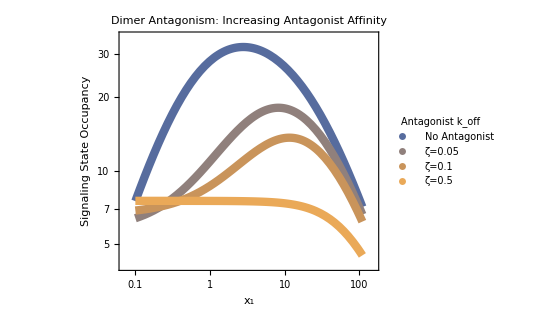

```mathematica
pops={Frame->{{True,False},{True,False}},FrameLabel->{"x_1","Signaling State Occupancy"},PlotLabel->"Dimer Antagonism:\nIncreasing Antagonist Affinity",PlotStyle->Join[Table[{contourcmap[[i]],Thickness[0.015]},{i,1,6}],{{Black,Dashed,Thickness[0.015]}}],AspectRatio->0.8,ImageSize->400,TicksStyle->Black,LabelStyle-> {Black,FontSize->20},Axes->{True,False}
};

FigS4C=Legended[
LogLogPlot[
{DiMixedSimple[0.1x1,0,0.1,0.2,100,1,0.01],
DiMixedSimple[0.1x1,10,0.1,2,100,1,0.01],
DiMixedSimple[0.1x1,10,0.1,1,100,1,0.01],
DiMixedSimple[0.1x1,10,0.1,0.2,100,1,0.01]},{x1,0.1,110},Evaluate@pops],

PointLegend[Table[contourcmap[[i]],{i,1,6}],{"No Antagonist","ζ=0.05","ζ=0.1","ζ=0.5"},LegendMarkerSize->25,LegendLabel->"Antagonist k_off",LabelStyle->{Directive[FontSize->20]}]]
```

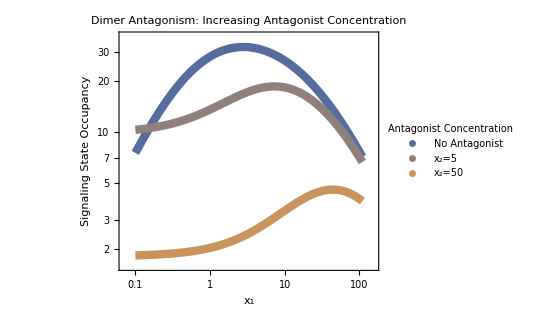

```mathematica
pops={Frame->{{True,False},{True,False}},FrameLabel->{"x_1","Signaling State Occupancy"},PlotLabel->"Dimer Antagonism:\nIncreasing Antagonist Concentration",PlotStyle->Join[Table[{contourcmap[[i]],Thickness[0.015]},{i,1,6}],{{Black,Dashed,Thickness[0.015]}}],AspectRatio->0.8,ImageSize->400,TicksStyle->Black,LabelStyle-> {Black,FontSize->20},Axes->{True,False}
};

FigS4D=Legended[
LogLogPlot[
{DiMixedSimple[0.1x1,0,0.1,1,100,1,0.01],
DiMixedSimple[0.1x1,5,0.1,1,100,1,0.01],
DiMixedSimple[0.1x1,50,0.1,1,100,1,0.01]},{x1,0.1,110},Evaluate@pops],

PointLegend[Table[contourcmap[[i]],{i,1,6}],{"No Antagonist","x_2=5","x_2=50"},LegendMarkerSize->25,LegendLabel->"Antagonist Concentration",LabelStyle->{Directive[FontSize->20]}]]
```

```mathematica
Row[{FigS4A,FigS4B}]
Row[{FigS4C,FigS4D}]
```

-Graphics--Graphics-

-Graphics--Graphics-

### Figure S5 (Non-equilibrium driving)

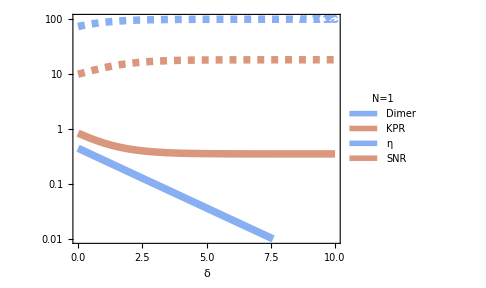

```mathematica
p1={kp->1,t->100,kon->1,c->0.001,RT->200,koff->1,kf->0.005,δ02->δTEST,δ03->δTEST,δ21->δTEST,δ32->δTEST,δ12->δTEST};
p2={kp->1,t->100,kon->1,c->0.001,RT->100,koff->1,kf->1,δ02->δTEST,δ03->δTEST,δ21->δTEST,δ32->δTEST,δ12->δTEST};
leg=LineLegend[{bigrad[[3]],bigrad[[7]],bigrad[[3]],bigrad[[7]]},{"Dimer","KPR","η","SNR"},LegendFunction->"Frame",LegendLabel->"N=1",BaseStyle->{{AbsoluteThickness[5],Dashed},{AbsoluteThickness[5],Dashed},{AbsoluteThickness[5]},{AbsoluteThickness[5]}}];

FigEntropyA=Show[
Legended[LogPlot[{SNRDimerNonEq/.p1,μN1NonEq/(√σ2N1NonEq)/.p2},{δTEST,0,10},Frame->{{True,False},{True,False}},FrameLabel->{"δ",None},FrameStyle->Black,LabelStyle->{Black,FontSize->24},ImageSize->Medium,AspectRatio->0.8,PlotStyle->Evaluate[{Thickness[0.015],#}&/@{bigrad[[3]],bigrad[[7]]}],PlotRange->{{0,10},{0.01,100}}],
leg],


(* η plots *)

LogPlot[R2KPR1[c,kon,0.1koff,kf,δ21,δ02,RT]/R2KPR1[c,kon,koff,kf,δ21,δ02,RT]/.p2,{δTEST,0,10},PlotStyle->{Thickness[0.015],bigrad[[7]],Dashed},PlotRange->{{0,10},{0.01,100}}],

LogPlot[TNonEq[c,RT,(0.1koff)/kon,(0.1 koff)/kf,δ12]/TNonEq[c,RT,koff/kon,koff/kf,δ12]/.p1,{δTEST,0,10},PlotStyle->{Thickness[0.015],bigrad[[3]],Dashed},PlotRange->{{0,10},{0.01,100}}]
]
```

## Approximate Expressions

### SNR in high g limit

```mathematica
asmps={x>0&&g>0&&RT>0&&δ21>0&&koff>0&&kon>0&&kp>0&&t>0&&Element[x|g|RT|δ21|koff|kon|kp|t,Reals],(ⅇ^(2 δ21) koff^2 (1+x)^2)/kon^2>0,((1+ⅇ^-δ21) kf+c (-1-ⅇ^-δ02) kon)^2>0};
```

#### Dimer

```mathematica
t1=Simplify[SNRDimerNonEq/.contractParams,Assumptions->asmps];

Assuming[asmps,Simplify[Series[Evaluate[t1/.g->1/q],{q,0,1}]]]


Assuming[asmps,Simplify[Series[t1,{g,0,1}]]]
```

(ⅇ^(-δ21/2) RT √((kp t x)/(1+kp t)) √q)/(1+x)+O[q]^(3/2)

(√(kp RT t))/(√2)-((ⅇ^(δ21/2) kp t (2+kp t+2 x)) √g)/(8 √(kp t x))+(ⅇ^δ21 kp t (4 kp t+3 kp^2 t^2+4 (1+x)^2) g)/(64 √2 √(kp RT t) x)+O[g]^(3/2)

```mathematica
(ⅇ^(-δ21/2)  x)/(√RT √(kp t (1+kp t) x g/RT) (1+x))
```